```mathematica
currDir=NotebookDirectory[];
Quiet[NotebookEvaluate[FileNameJoin[{currDir,"MIW_header_file.nb"}]]];
```

Epsilon divergences for perp integrals with non-zero masses

div A0: 2/((D-4) π)

div A1: 0

div A00: m10/((D-4) π)

div A11: 0

div A001: 0

div A111: 0

div A0000: m10^2/(4 (D-4) π)

div A0011: 0

div A1111: 0

div A00001: 0

div A00111: 0

div A11111: 0

div B0: 0

div B1: 0

div B00: 1/((D-4) π)

div B11: 0

div B001: -1/(2 (D-4) π)

div B111: 0

div B0000: (3 (m10+m20)-p10)/(12 (D-4) π)

div B0011: 1/(3 (D-4) π)

div B1111: 0

div B00001: (-2 m10-4 m20+p10)/(24 (D-4) π)

div B00111: -1/(4 (D-4) π)

div B11111: 0

```mathematica
timeLimit=0.5;(* in minutes *)(* set this higher overnight *)
timeLimit=timeLimit*60;
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

```mathematica
$HistoryLength=2;
$Assumptions=0<eps<1 && 0<M<1 &&pm>0&&pp>0&& 0<p1m<Q&&0<p1p<Q&&0<p2m<Q&&0<p2p<Q&&0<qm<Q&&0<qp<Q&&u∈Reals&&u=!=0&&kp∈Reals&&km∈Reals&&0≤ x≤ 1&&0≤ y≤ 1&&0≤ z≤ 1&&0≤ w≤ 1&&p3p∈Reals&&p3m∈Reals&&p4p∈Reals&&p4m∈Reals&&lambda∈Reals&&Q>0&&1/3>tau>0&&0<eta1&&0<eta2&&0<xi1<0.1&&0<xi2<0.1&&-1<a<2&&r>0&&km>0&&kp>0&&tau>0&&eta>0&&eta1>0&&eta2>0&&mb>0&&kp>0&&x>0&&0<xbar<1;

replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{tau,1,tau}]/.PlusDistribution[a_]:>HeavisideTheta[tau-beta]a+DiracDelta[tau-beta]Integrate[a,{tau,1,tau}];
```

```mathematica
(* this notebook needs a cleanup. the best section is probably the braodening with chiu, so just copy that and use it for thrust *)
```

```mathematica
83Pi^4/360/.Pi^4->(6zeta2)^2
11Pi^4/45/.Pi^4->(6zeta2)^2


83Pi^4/360/.Pi^4->(90zeta4)
```

(83 ζ_2^2)/10

(44 ζ_2^2)/5

(83 zeta4)/4

```mathematica
11Pi^2/9/.Pi^2->(6zeta2)
337Pi^2/108/.Pi^2->(6zeta2)
4Pi^2/9/.Pi^2->(6zeta2)
23Pi^2/27/.Pi^2->(6zeta2)
```

(22 ζ_2)/3

(337 ζ_2)/18

(8 ζ_2)/3

(46 ζ_2)/9

```mathematica
Zeta[4]//N
%/Zeta[2]
%//FullSimplify
```

1.08232

0.657974

0.657974

```mathematica
wilsonCoeffC2=1+alphaMS*Cf*(-8+(7*Pi^2)/6-3*Log[muMS^2/Q^2]-Log[muMS^2/Q^2]^2)/(4*Pi)
hardFunc=Series[wilsonCoeffC2^2,{alphaMS,0,1}]//Normal

wilsonCoeffC2NNLO=1+(alphaMS/(4*Pi))Cf*H0+(alphaMS/(4*Pi))^2*Cf*(Cf*HF1+Ca*HA1+Tf*Nf*Hf1);

H0=-L^2+3L-8+zeta2;

HF1=L^4/2-3L^3+(25/2-zeta2)L^2+(24*Zeta[3]-45/2-9zeta2)L+(255/8+21zeta2-83zeta2^2/10-30Zeta[3]);
HA1=11L^3/9+(2zeta2-233/18)L^2+(2545/54+22zeta2/3-26Zeta[3])L+(313Zeta[3]/9-51157/648-337zeta2/18+44*zeta2^2/5);
Hf1=-4L^3/9+38L^2/9-(8zeta2/3+418/27)L+(4085/162+46zeta2/9+4Zeta[3]/9);
hardFuncNNLO=Series[wilsonCoeffC2NNLO^2,{alphaMS,0,2}]//Normal


thrustAnswer = 1 + alphaMS*Cf*(-2Log[tau]^2 -3*Log[tau]+2*Pi^2/6-1)/(2*Pi)
answerBroad=1+alphaMS*Cf*(-8Log[tau]^2-12Log[tau]+2*Pi^2-14)/(4*Pi)

answerBroadNNLO=(1+Cbroad1(alphaMS/(2*Pi))+Cbroad2(alphaMS/(2*Pi))^2)*Exp[G12*(alphaMS/(2*Pi))*Log[1/tau]^2+G11*(alphaMS/(2*Pi))*Log[1/tau]^1+G10*(alphaMS/(2*Pi))*Log[1/tau]^0 +G23*(alphaMS/(2*Pi))^2*Log[1/tau]^3+G22*(alphaMS/(2*Pi))^2*Log[1/tau]^2+G21*(alphaMS/(2*Pi))^2*Log[1/tau]^1]

Cbroad1=(6zeta2-17/2)Cf;
Cbroad2=0;

G12=-4Cf;
G11=6Cf;
G10=3Cf/2;

G23=32Cf*Ta*Nf/9-88Ca*Cf/9;
G22=(4zeta2-35/9)Ca*Cf+4Cf*Ta*Nf/9-(16zeta2+32Log[2]^2)Cf^2;
G21=Cf^2(40Zeta[3]-45/2+24zeta2+128Log[2]^3/3+48Log[2]^2-64zeta2*Log[2])+Cf*Ca*(8*Zeta[3]-172G/3+109/18+22zeta2+64Log[2]^3/3+88Log[2]^2/3+256Log[2]/9-24zeta2*Log[2])+Cf*Ta*Nf*(56G/3-10/9-8zeta2-32Log[2]^2/3-80Log[2]/9);
```

(C_F α_OverBar[MS] (-log^2(μ_OverBar[MS]^2/Q^2)-3 log(μ_OverBar[MS]^2/Q^2)+(7 π^2)/6-8))/(4 π)+1

(α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)+1

α_OverBar[MS]^2 (1/(25920 π^2)C_F (28512 ζ_2^2 C_A-60660 ζ_2 C_A+3960 L^3 C_A+6480 ζ_2 L^2 C_A-41940 L^2 C_A+23760 ζ_2 L C_A-84240 L 3 C_A+152700 L C_A+112680 3 C_A-255785 C_A-26892 ζ_2^2 C_F+68040 ζ_2 C_F+1620 L^4 C_F-9720 L^3 C_F-3240 ζ_2 L^2 C_F+40500 L^2 C_F-29160 ζ_2 L C_F+77760 L 3 C_F-72900 L C_F-97200 3 C_F+103275 C_F-1440 L^3 N_f T_f+13680 L^2 N_f T_f-8640 ζ_2 L N_f T_f-50160 L N_f T_f+16560 ζ_2 N_f T_f+1440 3 N_f T_f+81700 N_f T_f)+(C_F^2 (ζ_2-L^2+3 L-8)^2)/(16 π^2))+(C_F (ζ_2-L^2+3 L-8) α_OverBar[MS])/(2 π)+1

(C_F α_OverBar[MS] (-2 log^2(τ)-3 log(τ)+π^2/3-1))/(2 π)+1

(C_F α_OverBar[MS] (-8 log^2(τ)-12 log(τ)+2 π^2-14))/(4 π)+1

(((6 ζ_2-17/2) C_F α_OverBar[MS])/(2 π)+1) exp((α_OverBar[MS]^2 log(1/τ) (T^a C_F N_f (-8 ζ_2+(56 G)/3-10/9-(32 log^2(2))/3-(80 log(2))/9)+C_A C_F (22 ζ_2-24 ζ_2 log(2)-(172 G)/3+8 3+109/18+(64 log^3(2))/3+(88 log^2(2))/3+(256 log(2))/9)+C_F^2 (24 ζ_2-64 ζ_2 log(2)+40 3-45/2+(128 log^3(2))/3+48 log^2(2))))/(4 π^2)+(α_OverBar[MS]^2 log^2(1/τ) (4/9 T^a C_F N_f+(4 ζ_2-35/9) C_A C_F+C_F^2 (-(16 ζ_2+32 log^2(2)))))/(4 π^2)+(α_OverBar[MS]^2 log^3(1/τ) (32/9 T^a C_F N_f-(88 C_A C_F)/9))/(4 π^2)-(2 C_F α_OverBar[MS] log^2(1/τ))/π+(3 C_F α_OverBar[MS] log(1/τ))/π+(3 C_F α_OverBar[MS])/(4 π))

```mathematica
scetAnswerBroad=Series[answerBroadNNLO/hardFuncNNLO,{alphaMS,0,2}]//Normal
%/.alphaMS->alphabar*2*Pi//Simplify
nnloAns=%/.L->2(Log[Q]-Log[muMS])//Expand
FullSimplify[%,Assumptions->muMS>0&&Q>0&&tau>0]
```

α_OverBar[MS]^2 (1/2 (2 ((log(1/τ) (T^a C_F N_f (-8 ζ_2+(56 G)/3-10/9-(32 log^2(2))/3-(80 log(2))/9)+C_A C_F (22 ζ_2-24 ζ_2 log(2)-(172 G)/3+8 3+109/18+(64 log^3(2))/3+(88 log^2(2))/3+(256 log(2))/9)+C_F^2 (24 ζ_2-64 ζ_2 log(2)+40 3-45/2+(128 log^3(2))/3+48 log^2(2))))/(4 π^2)-(log^2(1/τ) (-4 T^a C_F N_f-36 ζ_2 C_A C_F+35 C_A C_F+144 ζ_2 C_F^2+288 log^2(2) C_F^2))/(36 π^2)-(2 (11 C_A C_F log^3(1/τ)-4 T^a C_F N_f log^3(1/τ)))/(9 π^2))+((-8 C_F log^2(1/τ)+12 C_F log(1/τ)+3 C_F)^2)/(16 π^2))+1/(25920 π^2)(-28512 ζ_2^2 C_A C_F+60660 ζ_2 C_A C_F-3960 L^3 C_A C_F-6480 ζ_2 L^2 C_A C_F+41940 L^2 C_A C_F-23760 ζ_2 L C_A C_F+84240 L 3 C_A C_F-152700 L C_A C_F-112680 3 C_A C_F+255785 C_A C_F+1440 L^3 C_F N_f T_f-13680 L^2 C_F N_f T_f+8640 ζ_2 L C_F N_f T_f+50160 L C_F N_f T_f-16560 ζ_2 C_F N_f T_f-1440 3 C_F N_f T_f-81700 C_F N_f T_f+31752 ζ_2^2 C_F^2-145800 ζ_2 C_F^2+3240 L^4 C_F^2-19440 L^3 C_F^2-6480 ζ_2 L^2 C_F^2+81000 L^2 C_F^2+58320 ζ_2 L C_F^2-77760 L 3 C_F^2-160380 L C_F^2+97200 3 C_F^2+207765 C_F^2)+((12 ζ_2-17) C_F (-8 C_F log^2(1/τ)+12 C_F log(1/τ)+3 C_F))/(16 π^2)+((-ζ_2 C_F+L^2 C_F-3 L C_F+8 C_F) (((12 ζ_2-17) C_F)/(4 π)+(-8 C_F log^2(1/τ)+12 C_F log(1/τ)+3 C_F)/(4 π)))/(2 π))+(α_OverBar[MS] (5 ζ_2 C_F+L^2 C_F-3 L C_F-4 C_F log^2(1/τ)+6 C_F log(1/τ)+C_F))/(2 π)+1

1/6480(ᾱ)^2 C_F (360 log(τ) (4 T^a N_f (36 ζ_2-84 G+5+48 log^2(2)+40 log(2))+C_A (-396 ζ_2+432 ζ_2 log(2)+1032 G-144 3-109-384 log^3(2)-528 log^2(2)-512 log(2))-3 C_F (324 ζ_2-384 ζ_2 log(2)+36 L^2-108 L+240 3-99+256 log^3(2)+288 log^2(2)))+720 log^2(τ) (4 T^a N_f+(36 ζ_2-35) C_A-18 C_F (18 ζ_2+2 L^2-6 L-7+16 log^2(2)))+5760 log^3(τ) (-4 T^a N_f+11 C_A+27 C_F)-C_A (28512 ζ_2^2-60660 ζ_2+3960 L^3+180 (36 ζ_2-233) L^2+60 L (396 ζ_2-1404 3+2545)+112680 3-255785)-7128 ζ_2^2 C_F+268920 ζ_2 C_F+3240 L^4 C_F-19440 L^3 C_F+32400 ζ_2 L^2 C_F+35640 L^2 C_F-58320 ζ_2 L C_F-77760 L 3 C_F-24300 L C_F+51840 C_F log^4(τ)+97200 3 C_F-230445 C_F+1440 L^3 N_f T_f-13680 L^2 N_f T_f+8640 ζ_2 L N_f T_f+50160 L N_f T_f-16560 ζ_2 N_f T_f-1440 3 N_f T_f-81700 N_f T_f)+ᾱ C_F (5 ζ_2+L^2-3 L-4 log^2(τ)-6 log(τ)+1)+1

8 C_F^2 (ᾱ)^2 log^4(μ_OverBar[MS])+24 C_F^2 (ᾱ)^2 log^3(μ_OverBar[MS])+44/9 C_A C_F (ᾱ)^2 log^3(μ_OverBar[MS])-16/9 C_F N_f T_f (ᾱ)^2 log^3(μ_OverBar[MS])-32 C_F^2 log(Q) (ᾱ)^2 log^3(μ_OverBar[MS])+22 C_F^2 (ᾱ)^2 log^2(μ_OverBar[MS])+48 C_F^2 log^2(Q) (ᾱ)^2 log^2(μ_OverBar[MS])-16 C_F^2 log^2(τ) (ᾱ)^2 log^2(μ_OverBar[MS])+233/9 C_A C_F (ᾱ)^2 log^2(μ_OverBar[MS])-76/9 C_F N_f T_f (ᾱ)^2 log^2(μ_OverBar[MS])+20 C_F^2 ζ_2 (ᾱ)^2 log^2(μ_OverBar[MS])-4 C_A C_F ζ_2 (ᾱ)^2 log^2(μ_OverBar[MS])-72 C_F^2 log(Q) (ᾱ)^2 log^2(μ_OverBar[MS])-44/3 C_A C_F log(Q) (ᾱ)^2 log^2(μ_OverBar[MS])+16/3 C_F N_f T_f log(Q) (ᾱ)^2 log^2(μ_OverBar[MS])-24 C_F^2 log(τ) (ᾱ)^2 log^2(μ_OverBar[MS])+4 C_F ᾱ log^2(μ_OverBar[MS])-32 C_F^2 log^3(Q) (ᾱ)^2 log(μ_OverBar[MS])+15/2 C_F^2 (ᾱ)^2 log(μ_OverBar[MS])+72 C_F^2 log^2(Q) (ᾱ)^2 log(μ_OverBar[MS])+44/3 C_A C_F log^2(Q) (ᾱ)^2 log(μ_OverBar[MS])-16/3 C_F N_f T_f log^2(Q) (ᾱ)^2 log(μ_OverBar[MS])-24 C_F^2 log^2(τ) (ᾱ)^2 log(μ_OverBar[MS])+32 C_F^2 log(Q) log^2(τ) (ᾱ)^2 log(μ_OverBar[MS])+2545/54 C_A C_F (ᾱ)^2 log(μ_OverBar[MS])-418/27 C_F N_f T_f (ᾱ)^2 log(μ_OverBar[MS])+18 C_F^2 ζ_2 (ᾱ)^2 log(μ_OverBar[MS])+22/3 C_A C_F ζ_2 (ᾱ)^2 log(μ_OverBar[MS])-8/3 C_F N_f T_f ζ_2 (ᾱ)^2 log(μ_OverBar[MS])-44 C_F^2 log(Q) (ᾱ)^2 log(μ_OverBar[MS])-466/9 C_A C_F log(Q) (ᾱ)^2 log(μ_OverBar[MS])+152/9 C_F N_f T_f log(Q) (ᾱ)^2 log(μ_OverBar[MS])-40 C_F^2 ζ_2 log(Q) (ᾱ)^2 log(μ_OverBar[MS])+8 C_A C_F ζ_2 log(Q) (ᾱ)^2 log(μ_OverBar[MS])-36 C_F^2 log(τ) (ᾱ)^2 log(μ_OverBar[MS])+48 C_F^2 log(Q) log(τ) (ᾱ)^2 log(μ_OverBar[MS])+6 C_F ᾱ log(μ_OverBar[MS])-8 C_F log(Q) ᾱ log(μ_OverBar[MS])+24 C_F^2 (ᾱ)^2 3 log(μ_OverBar[MS])-26 C_A C_F (ᾱ)^2 3 log(μ_OverBar[MS])+8 C_F^2 log^4(Q) (ᾱ)^2+8 C_F^2 log^4(τ) (ᾱ)^2-24 C_F^2 log^3(Q) (ᾱ)^2-44/9 C_A C_F log^3(Q) (ᾱ)^2+16/9 C_F N_f T_f log^3(Q) (ᾱ)^2+24 C_F^2 log^3(τ) (ᾱ)^2+88/9 C_A C_F log^3(τ) (ᾱ)^2-32/9 C_F N_f T^a log^3(τ) (ᾱ)^2-569/16 C_F^2 (ᾱ)^2-11/10 C_F^2 ζ_2^2 (ᾱ)^2-22/5 C_A C_F ζ_2^2 (ᾱ)^2+22 C_F^2 log^2(Q) (ᾱ)^2+233/9 C_A C_F log^2(Q) (ᾱ)^2-76/9 C_F N_f T_f log^2(Q) (ᾱ)^2+20 C_F^2 ζ_2 log^2(Q) (ᾱ)^2-4 C_A C_F ζ_2 log^2(Q) (ᾱ)^2+14 C_F^2 log^2(τ) (ᾱ)^2-16 C_F^2 log^2(Q) log^2(τ) (ᾱ)^2-35/9 C_A C_F log^2(τ) (ᾱ)^2+4/9 C_F N_f T^a log^2(τ) (ᾱ)^2-36 C_F^2 ζ_2 log^2(τ) (ᾱ)^2+4 C_A C_F ζ_2 log^2(τ) (ᾱ)^2+24 C_F^2 log(Q) log^2(τ) (ᾱ)^2-32 C_F^2 log^2(2) log^2(τ) (ᾱ)^2+(51157 C_A C_F (ᾱ)^2)/1296-4085/324 C_F N_f T_f (ᾱ)^2+83/2 C_F^2 ζ_2 (ᾱ)^2+337/36 C_A C_F ζ_2 (ᾱ)^2-23/9 C_F N_f T_f ζ_2 (ᾱ)^2-15/2 C_F^2 log(Q) (ᾱ)^2-2545/54 C_A C_F log(Q) (ᾱ)^2+418/27 C_F N_f T_f log(Q) (ᾱ)^2-18 C_F^2 ζ_2 log(Q) (ᾱ)^2-22/3 C_A C_F ζ_2 log(Q) (ᾱ)^2+8/3 C_F N_f T_f ζ_2 log(Q) (ᾱ)^2+33/2 C_F^2 log(τ) (ᾱ)^2-24 C_F^2 log^2(Q) log(τ) (ᾱ)^2-109/18 C_A C_F log(τ) (ᾱ)^2+172/3 C_A C_F G log(τ) (ᾱ)^2+10/9 C_F N_f T^a log(τ) (ᾱ)^2-56/3 C_F G N_f T^a log(τ) (ᾱ)^2-54 C_F^2 ζ_2 log(τ) (ᾱ)^2-22 C_A C_F ζ_2 log(τ) (ᾱ)^2+8 C_F N_f T^a ζ_2 log(τ) (ᾱ)^2+36 C_F^2 log(Q) log(τ) (ᾱ)^2-128/3 C_F^2 log^3(2) log(τ) (ᾱ)^2-64/3 C_A C_F log^3(2) log(τ) (ᾱ)^2-48 C_F^2 log^2(2) log(τ) (ᾱ)^2-88/3 C_A C_F log^2(2) log(τ) (ᾱ)^2+32/3 C_F N_f T^a log^2(2) log(τ) (ᾱ)^2-256/9 C_A C_F log(2) log(τ) (ᾱ)^2+80/9 C_F N_f T^a log(2) log(τ) (ᾱ)^2+64 C_F^2 ζ_2 log(2) log(τ) (ᾱ)^2+24 C_A C_F ζ_2 log(2) log(τ) (ᾱ)^2+4 C_F log^2(Q) ᾱ-4 C_F log^2(τ) ᾱ+C_F ᾱ+5 C_F ζ_2 ᾱ-6 C_F log(Q) ᾱ-6 C_F log(τ) ᾱ+15 C_F^2 (ᾱ)^2 3-313/18 C_A C_F (ᾱ)^2 3-2/9 C_F N_f T_f (ᾱ)^2 3-24 C_F^2 log(Q) (ᾱ)^2 3+26 C_A C_F log(Q) (ᾱ)^2 3-40 C_F^2 log(τ) (ᾱ)^2 3-8 C_A C_F log(τ) (ᾱ)^2 3+1

$Aborted

```mathematica
SeriesCoefficient[nnloAns,{Cf,0,2},{alphabar,0,2}]
%/.Log[Q]->(2LJ-LS)/2+Log[muMS]//Expand
%//Simplify
%/.Log[tau]->LS-LJ//Simplify
%//Expand

SeriesCoefficient[nnloAns,{Tf,0,1},{alphabar,0,2}]
%/.Log[Q]->(2LJ-LS)/2+Log[muMS]//Expand
%//Simplify
%/.Log[tau]->LS-LJ//Simplify
%//Expand
```

1/240 (-8640 ζ_2 log^2(τ)-12960 ζ_2 log(τ)+15360 ζ_2 log(2) log(τ)-264 ζ_2^2+9960 ζ_2-9600 ζ_2 log(Q) log(μ_OverBar[MS])+7680 log(Q) log^2(τ) log(μ_OverBar[MS])+11520 log(Q) log(τ) log(μ_OverBar[MS])-7680 log(Q) log^3(μ_OverBar[MS])-7680 log^3(Q) log(μ_OverBar[MS])+11520 log^2(Q) log^2(μ_OverBar[MS])-17280 log(Q) log^2(μ_OverBar[MS])+17280 log^2(Q) log(μ_OverBar[MS])-10560 log(Q) log(μ_OverBar[MS])+4800 ζ_2 log^2(μ_OverBar[MS])+4320 ζ_2 log(μ_OverBar[MS])-3840 log^2(τ) log^2(μ_OverBar[MS])-5760 log(τ) log^2(μ_OverBar[MS])-5760 log^2(τ) log(μ_OverBar[MS])-8640 log(τ) log(μ_OverBar[MS])+5760 3 log(μ_OverBar[MS])+1920 log^4(μ_OverBar[MS])+5760 log^3(μ_OverBar[MS])+5280 log^2(μ_OverBar[MS])+1800 log(μ_OverBar[MS])+4800 ζ_2 log^2(Q)-4320 ζ_2 log(Q)-3840 log^2(Q) log^2(τ)+5760 log(Q) log^2(τ)-5760 log^2(Q) log(τ)+8640 log(Q) log(τ)-5760 3 log(Q)+1920 log^4(Q)-5760 log^3(Q)+5280 log^2(Q)-1800 log(Q)+1920 log^4(τ)+5760 log^3(τ)-10240 log^3(2) log(τ)-7680 log^2(2) log^2(τ)+3360 log^2(τ)-11520 log^2(2) log(τ)+3960 log(τ)-9600 3 log(τ)+3600 3-8535)

-36 ζ_2 log^2(τ)-54 ζ_2 log(τ)+64 ζ_2 log(2) log(τ)-(11 ζ_2^2)/10+(83 ζ_2)/2+8 LJ^4-16 LJ^3 LS-24 LJ^3+20 ζ_2 LJ^2+12 LJ^2 LS^2+36 LJ^2 LS-16 LJ^2 log^2(τ)-24 LJ^2 log(τ)+22 LJ^2-18 ζ_2 LJ-4 LJ LS^3-18 LJ LS^2-20 ζ_2 LJ LS+16 LJ LS log^2(τ)+24 LJ LS log(τ)-22 LJ LS+24 LJ log^2(τ)+36 LJ log(τ)-24 LJ 3-(15 LJ)/2+LS^4/2+3 LS^3+5 ζ_2 LS^2-4 LS^2 log^2(τ)-6 LS^2 log(τ)+(11 LS^2)/2+9 ζ_2 LS-12 LS log^2(τ)-18 LS log(τ)+12 LS 3+(15 LS)/4+8 log^4(τ)+24 log^3(τ)-128/3 log^3(2) log(τ)-32 log^2(2) log^2(τ)+14 log^2(τ)-48 log^2(2) log(τ)+(33 log(τ))/2-40 3 log(τ)+15 3-569/16

-(11 ζ_2^2)/10+(83 ζ_2)/2+8 LJ^4-8 LJ^3 (2 LS+3)-2 log^2(τ) (18 ζ_2+8 LJ^2-4 LJ (2 LS+3)+2 LS^2+6 LS-7+16 log^2(2))+2 LJ^2 (10 ζ_2+6 LS^2+18 LS+11)+log(τ) (-54 ζ_2+64 ζ_2 log(2)-24 LJ^2+12 LJ (2 LS+3)-6 LS^2-18 LS-40 3+33/2-(128 log^3(2))/3-48 log^2(2))-1/2 LJ (36 ζ_2+8 LS^3+36 LS^2+40 ζ_2 LS+44 LS+48 3+15)+LS^4/2+3 LS^3+5 ζ_2 LS^2+(11 LS^2)/2+9 ζ_2 LS+12 LS 3+(15 LS)/4+8 log^4(τ)+24 log^3(τ)+15 3-569/16

-(11 ζ_2^2)/10+(83 ζ_2)/2+8 LJ^2 (LS^2-2 (ζ_2+2 log^2(2)))+4/3 LJ (27 ζ_2-48 ζ_2 log(2)-9 LS^3-9 LS^2+LS (39 ζ_2+3+48 log^2(2))+12 3-18+32 log^3(2)+36 log^2(2))+(9 LS^4)/2+9 LS^3+LS^2 (-31 ζ_2+3/2-32 log^2(2))+LS (-45 ζ_2+64 ζ_2 log(2)-28 3+81/4-(128 log^3(2))/3-48 log^2(2))+15 3-569/16

-(11 ζ_2^2)/10+(83 ζ_2)/2-16 ζ_2 LJ^2+8 LJ^2 LS^2-32 LJ^2 log^2(2)+36 ζ_2 LJ-64 ζ_2 LJ log(2)-12 LJ LS^3-12 LJ LS^2+52 ζ_2 LJ LS+4 LJ LS+64 LJ LS log^2(2)+16 LJ 3-24 LJ+128/3 LJ log^3(2)+48 LJ log^2(2)+(9 LS^4)/2+9 LS^3-31 ζ_2 LS^2+(3 LS^2)/2-32 LS^2 log^2(2)-45 ζ_2 LS+64 ζ_2 LS log(2)-28 LS 3+(81 LS)/4-128/3 LS log^3(2)-48 LS log^2(2)+15 3-569/16

1/324 (-828 ζ_2 C_F N_f+1728 C_F N_f log(Q) log^2(μ_OverBar[MS])-1728 C_F N_f log^2(Q) log(μ_OverBar[MS])+5472 C_F N_f log(Q) log(μ_OverBar[MS])-864 ζ_2 C_F N_f log(μ_OverBar[MS])-576 C_F N_f log^3(μ_OverBar[MS])-2736 C_F N_f log^2(μ_OverBar[MS])-5016 C_F N_f log(μ_OverBar[MS])+864 ζ_2 C_F N_f log(Q)+576 C_F N_f log^3(Q)-2736 C_F N_f log^2(Q)+5016 C_F N_f log(Q)-72 3 C_F N_f-4085 C_F N_f)

16/9 LJ^3 C_F N_f-8/3 LJ^2 LS C_F N_f-76/9 LJ^2 C_F N_f+4/3 LJ LS^2 C_F N_f+76/9 LJ LS C_F N_f+8/3 ζ_2 LJ C_F N_f+418/27 LJ C_F N_f-2/9 LS^3 C_F N_f-19/9 LS^2 C_F N_f-4/3 ζ_2 LS C_F N_f-209/27 LS C_F N_f-23/9 ζ_2 C_F N_f-2/9 3 C_F N_f-(4085 C_F N_f)/324

1/324 C_F N_f (-828 ζ_2+576 LJ^3-144 LJ^2 (6 LS+19)+24 LJ (36 ζ_2+18 LS^2+114 LS+209)-72 LS^3-684 LS^2-12 (36 ζ_2+209) LS-72 3-4085)

1/324 C_F N_f (-828 ζ_2+576 LJ^3-144 LJ^2 (6 LS+19)+24 LJ (36 ζ_2+18 LS^2+114 LS+209)-72 LS^3-684 LS^2-12 (36 ζ_2+209) LS-72 3-4085)

16/9 LJ^3 C_F N_f-8/3 LJ^2 LS C_F N_f-76/9 LJ^2 C_F N_f+4/3 LJ LS^2 C_F N_f+76/9 LJ LS C_F N_f+8/3 ζ_2 LJ C_F N_f+418/27 LJ C_F N_f-2/9 LS^3 C_F N_f-19/9 LS^2 C_F N_f-4/3 ζ_2 LS C_F N_f-209/27 LS C_F N_f-23/9 ζ_2 C_F N_f-2/9 3 C_F N_f-(4085 C_F N_f)/324

```mathematica
answerBroadNNLO
Series[answerBroadNNLO,{alphaMS,0,1}]//Normal;
%/.alphaMS->alphabar*2*Pi//Simplify
Series[answerBroadNNLO,{alphaMS,0,2}]//Normal;
%/.alphaMS->alphabar*2*Pi//Simplify
```

(((6 ζ_2-17/2) C_F α_OverBar[MS])/(2 π)+1) exp((α_OverBar[MS]^2 log(1/τ) (T^a C_F N_f (-8 ζ_2+(56 G)/3-10/9-(32 log^2(2))/3-(80 log(2))/9)+C_A C_F (22 ζ_2-24 ζ_2 log(2)-(172 G)/3+8 3+109/18+(64 log^3(2))/3+(88 log^2(2))/3+(256 log(2))/9)+C_F^2 (24 ζ_2-64 ζ_2 log(2)+40 3-45/2+(128 log^3(2))/3+48 log^2(2))))/(4 π^2)+(α_OverBar[MS]^2 log^2(1/τ) (4/9 T^a C_F N_f+(4 ζ_2-35/9) C_A C_F+C_F^2 (-(16 ζ_2+32 log^2(2)))))/(4 π^2)+(α_OverBar[MS]^2 log^3(1/τ) (32/9 T^a C_F N_f-(88 C_A C_F)/9))/(4 π^2)-(2 C_F α_OverBar[MS] log^2(1/τ))/π+(3 C_F α_OverBar[MS] log(1/τ))/π+(3 C_F α_OverBar[MS])/(4 π))

ᾱ C_F (6 ζ_2-4 log^2(τ)-6 log(τ)-7)+1

1/72 (ᾱ)^2 C_F (4 log(τ) (4 T^a N_f (36 ζ_2-84 G+5+48 log^2(2)+40 log(2))+C_A (-396 ζ_2+432 ζ_2 log(2)+1032 G-144 3-109-384 log^3(2)-528 log^2(2)-512 log(2))-3 C_F (ζ_2 (360-384 log(2))+240 3-387+256 log^3(2)+288 log^2(2)))+8 log^2(τ) (4 T^a N_f+(36 ζ_2-35) C_A-18 C_F (20 ζ_2-23+16 log^2(2)))+64 log^3(τ) (-4 T^a N_f+11 C_A+27 C_F)+27 (24 ζ_2-31) C_F+576 C_F log^4(τ))+ᾱ C_F (6 ζ_2-4 log^2(τ)-6 log(τ)-7)+1

```mathematica
answerBroad/(wilsonCoeffC2^2)
Series[%,{alphaMS,0,1}]//Normal
%/.Log[tau]->(L2-LQ)/2/.Log[muMS^2/Q^2]->-LQ//Simplify
%/.alphaMS->alphabar*2*Pi/Cf//Expand
%//Simplify
%/.LQ->(4L1-L4)/3//Expand
%/.L2->(2L1+L4)/3
%//Simplify//Expand
```

((C_F α_OverBar[MS] (-8 log^2(τ)-12 log(τ)+2 π^2-14))/(4 π)+1)/(((C_F α_OverBar[MS] (-log^2(μ_OverBar[MS]^2/Q^2)-3 log(μ_OverBar[MS]^2/Q^2)+(7 π^2)/6-8))/(4 π)+1)^2)

(α_OverBar[MS] (6 C_F log^2(μ_OverBar[MS]^2/Q^2)+18 C_F log(μ_OverBar[MS]^2/Q^2)-24 C_F log^2(τ)-36 C_F log(τ)+6 C_F-π^2 C_F))/(12 π)+1

(12 π-C_F (6 L2^2-6 L2 (2 LQ-3)+π^2-6) α_OverBar[MS])/(12 π)

-(π^2 ᾱ)/6+ᾱ+L2^2 (-ᾱ)-3 L2 ᾱ+2 L2 LQ ᾱ+1

ᾱ (-L2^2+L2 (2 LQ-3)-π^2/6+1)+1

-(π^2 ᾱ)/6+ᾱ+8/3 L1 L2 ᾱ+L2^2 (-ᾱ)-3 L2 ᾱ-2/3 L2 L4 ᾱ+1

-(π^2 ᾱ)/6+ᾱ-1/9 ᾱ (2 L1+L4)^2+8/9 L1 ᾱ (2 L1+L4)-2/9 L4 ᾱ (2 L1+L4)-ᾱ (2 L1+L4)+1

-(π^2 ᾱ)/6+ᾱ+(4 L1^2 ᾱ)/3-2 L1 ᾱ-(L4^2 ᾱ)/3-L4 ᾱ+1

```mathematica
%/.L4->3L2-2L1//Expand
%//replShortLogs
```

-(π^2 ᾱ)/6+ᾱ+4 L1 L2 ᾱ-3 L2^2 ᾱ-3 L2 ᾱ+1

-(π^2 ᾱ)/6+ᾱ-3 ᾱ log^2((Q^2 τ^2)/μ_OverBar[MS]^2)+4 ᾱ log((Q^2 τ)/μ_OverBar[MS]^2) log((Q^2 τ^2)/μ_OverBar[MS]^2)-3 ᾱ log((Q^2 τ^2)/μ_OverBar[MS]^2)+1

```mathematica
%*L1//replShortLogs
```

log((Q^2 τ)/μ_OverBar[MS]^2) (-(π^2 ᾱ)/6+ᾱ-3 ᾱ log^2((b^2 Q^2)/μ_OverBar[MS]^2)+4 ᾱ log((b Q^2)/μ_OverBar[MS]^2) log((b^2 Q^2)/μ_OverBar[MS]^2)-3 ᾱ log((b^2 Q^2)/μ_OverBar[MS]^2)+1)

#### Heavy-Heavy Integration

```mathematica
amplitude=(kp*km)^(-eps)/(kp+km)^(2)//FullSimplify
heavyOnShell=UnitStep[kp*km]UnitStep[kp+km]UnitStep[  2 SPD[v,pb-x*mb*nb/2-k]   ]DiracDelta[mb^2-pbm(kp+x*mb)+km*(x*mb-pbp)]
%*amplitude//Simplify
igrand=%/.pbm->mb+qm/.pbp->mb+qp//Simplify
Integrate[igrand,{km,-Infinity,Infinity}]
heavyResult=FullSimplify[%,Assumptions->mb>0&&kp>0&&x>0]
```

((k^+ k^-)^-ϵ)/((k^++k^-)^2)

k^+ k^- k^++k^- (TraditionalForm`m)_B^2+k^- ((TraditionalForm`m)_B x-p_b^+)-((TraditionalForm`m)_B x+k^+) p_b^- 2 (-(1/2 k·(n+n̄))-1/2 (TraditionalForm`m)_B x ((n+n̄)/2)^-+1/2 (n+n̄)·p_b)

((k^+ k^-)^-ϵ (TraditionalForm`m)_B^2+k^- ((TraditionalForm`m)_B x-p_b^+)-((TraditionalForm`m)_B x+k^+) p_b^- -(TraditionalForm`m)_B x-k^+-k^-+p_b^++p_b^-)/((k^++k^-)^2)

((k^+ k^-)^-ϵ (TraditionalForm`m)_B^2+k^- ((TraditionalForm`m)_B (x-1)-q^+)-((TraditionalForm`m)_B x+k^+) ((TraditionalForm`m)_B+q^-) -x (TraditionalForm`m)_B+2 (TraditionalForm`m)_B-k^+-k^-+q^++q^-)/((k^++k^-)^2)

((-x m_B+m_B+q^+) -x (TraditionalForm`m)_B+2 (TraditionalForm`m)_B-k^++q^++q^-+((TraditionalForm`m)_B^2-((TraditionalForm`m)_B x+k^+) ((TraditionalForm`m)_B+q^-))/((TraditionalForm`m)_B (x-1)-q^+) (-(k^+ (m_B^2-(m_B+q^-) (x m_B+k^+)))/((x-1) m_B-q^+))^-ϵ)/((k^+ (x m_B-q^++q^-)+m_B ((x-1) m_B+q^- x))^2)

((-x m_B+m_B+q^+) -x (TraditionalForm`m)_B+2 (TraditionalForm`m)_B-k^++q^++q^-+((TraditionalForm`m)_B^2-((TraditionalForm`m)_B x+k^+) ((TraditionalForm`m)_B+q^-))/((TraditionalForm`m)_B (x-1)-q^+) (-(k^+ (m_B^2-(m_B+q^-) (x m_B+k^+)))/((x-1) m_B-q^+))^-ϵ)/((k^+ (x m_B-q^++q^-)+m_B ((x-1) m_B+q^- x))^2)

```mathematica
heavyResult
%/.mb->1//FullSimplify
%*(1-x)^(-1-eps)/.qp->0
%//FullSimplify
blah=Integrate[%*Boole[x*(kp+x-2)≥-1],{kp,0,Infinity}]
```

((-x m_B+m_B+q^+) -x (TraditionalForm`m)_B+2 (TraditionalForm`m)_B-k^++q^++q^-+((TraditionalForm`m)_B^2-((TraditionalForm`m)_B x+k^+) ((TraditionalForm`m)_B+q^-))/((TraditionalForm`m)_B (x-1)-q^+) (-(k^+ (m_B^2-(m_B+q^-) (x m_B+k^+)))/((x-1) m_B-q^+))^-ϵ)/((k^+ (x m_B-q^++q^-)+m_B ((x-1) m_B+q^- x))^2)

Piecewise[{{((q^+-x+1) ((k^+ (q^- (k^++x)+k^++x-1))/(-q^++x-1))^-ϵ)/((k^+ (-q^++q^-+x)+q^- x+x-1)^2), k^+ (-q^++q^-+x)+q^+ (q^++q^--2 x+3)+q^-+(x-1)^2≥0}, {0, True}}]

Piecewise[{{((1-x)^-ϵ ((k^+ (q^- (k^++x)+k^++x-1))/(x-1))^-ϵ)/((k^+ (q^-+x)+q^- x+x-1)^2), k^+ (q^-+x)+q^-+(x-1)^2≥0}, {0, True}}]

((-k^+ (q^- (k^++x)+k^++x-1))^-ϵ)/((k^+ (q^-+x)+q^- x+x-1)^2)

$Aborted

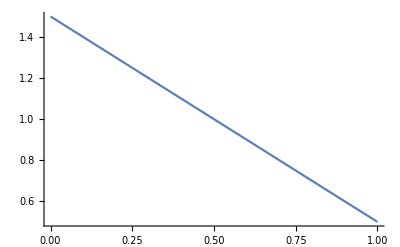

```mathematica
Plot[2-x-1/2,{x,0,1}]
```

```mathematica
blah/.x-1->-xbar/. 1-x->xbar//Expand
FullSimplify[%,Assumptions->1>xbar>0]
%/. xbar^(-1+a_):> -DiracDelta[xbar-delta]/(-a)+PlusDistribution[HeavisideTheta[xbar]/xbar]+a*PlusDistribution[HeavisideTheta[xbar]*Log[xbar]/xbar]
Series[%/.delta->0,{x,1,0}]//Normal
Series[%,{eps,0,0}]//Normal
```

{(x̄ ((k^+ (x̄-k^+))/(x̄))^-ϵ)/((k^+ x-x̄)^2),k^+ x+x^2-2 x+1≥0}

{((x̄)^(ϵ+1) (k^+ (x̄-k^+))^-ϵ)/((x̄-k^+ x)^2),k^+ x+(x-1)^2≥0}

{((x̄)^(ϵ+1) (k^+ (x̄-k^+))^-ϵ)/((x̄-k^+ x)^2),k^+ x+(x-1)^2≥0}

{((x̄)^(ϵ+1) (k^+ (x̄-k^+))^-ϵ)/((x̄-k^+)^2),k^+ x+(x-1)^2≥0}

{(x̄)/((x̄-k^+)^2),k^+ x+(x-1)^2≥0}

#### LO Thrust with Timelike Rapidity Regulator

```mathematica
igrand=1/((km+kp*xi1)(kp+km*xi2));
onShellDelta=DiracDelta[kp*km-r^2]HeavisideTheta[kp]HeavisideTheta[km];

(* the measurement function when k is in the positive hemisphere *)
measurementDelta1=Inactive[DiracDelta][tau-kp^(1-a/2)km^(a/2)]/.a->0;
Print["Total integrand 1 is:  ", HeavisideTheta[km-kp]igrand*onShellDelta*measurementDelta1];
preMeasure1=Integrate[ HeavisideTheta[km-kp]igrand*onShellDelta*measurementDelta1,{kp,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure1//Activate];
afterMeasure1=Integrate[FullSimplify[Activate[r^(D-3)preMeasure1]//piecewiseToBoole],{r,0,Infinity}];
afterMeasure1=afterMeasure1/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure1];
afterfinal1=Integrate[afterMeasure1,{km,0,Infinity}];
afterfinal1=Quiet[%/.D->4-2*eps//FullSimplify]


(* the measurement function when k is in the positive hemisphere *)
measurementDelta1=Inactive[DiracDelta][tau-km^(1-a/2)kp^(a/2)]/.a->0;
Print["Total integrand 2 is:  ", HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1];
preMeasure2=Integrate[ HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1,{km,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure2//Activate];
afterMeasure2=Integrate[FullSimplify[Activate[r^(D-3)preMeasure2]//piecewiseToBoole],{r,0,Infinity}];
afterMeasure2=afterMeasure2/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure2];
afterfinal2=Integrate[afterMeasure2,{kp,0,Infinity}];
afterfinal2=Quiet[%/.D->4-2*eps//FullSimplify]

result1=afterfinal1+afterfinal2
Limit[%,xi2->xi1]
result=Limit[%,xi1->0,Analytic->True]
```

Total integrand 1 is:  (r^2-k^+ k^- k^+ k^- k^--k^+ δ[τ-k^+])/((ξ_1 k^++k^-) (k^++ξ_2 k^-))

After on-shell condition:  Piecewise[{{(r^(D-3) τ-r^2/k^- k^-)/((ξ_1 r^2+(k^-)^2) (r^2+ξ_2 (k^-)^2)), r<k^-}, {0, True}}]

After measurement:  Piecewise[{{(Boole[√(τ k^-)<k^-] (τ k^-)^(D/2))/(2 τ^2 (k^-)^2 (ξ_1 τ+k^-) (τ+ξ_2 k^-)), Re(D)>-62}, {0, True}}]

$Aborted

$Aborted

Total integrand 2 is:  (r^2-k^+ k^- k^+ k^+-k^- k^- δ[τ-k^-])/((ξ_1 k^++k^-) (k^++ξ_2 k^-))

$Aborted

After on-shell condition:  preMeasure2 r^(D-3)

$Aborted

After measurement:  afterMeasure2

afterMeasure2 ∞

afterMeasure2 ∞+$Aborted

afterMeasure2 ∞+$Aborted

afterMeasure2 ∞+$Aborted

```mathematica
sigmaThrust=DiracDelta[tau-delta]+2(* this two is for both diagrams*)*alphaMS*4*Pi*Cf*(muMS^2*Exp[EulerGamma]/(4*Pi*Q^2))^eps*2*Pi^((D-2)/2)*result/(Gamma[(D-2)/2]*(2*Pi)^(D-1))
%/.D->4-2*eps
%/. tau^(-1+a_):> -DiracDelta[tau-delta]/(-a)+PlusDistribution[HeavisideTheta[tau]/tau]+a*PlusDistribution[HeavisideTheta[tau]*Log[tau]/tau]
Series[%,{eps,0,0}]//Normal
sigmaThrust=%(*//replSingVarPlus*)
diffCTermThrust=DiracDelta[tau-delta]+Series[sigmaThrust,{eps,0,-1}]//Normal
diffSoftResult=SeriesCoefficient[sigmaThrust,{eps,0,0}]//Normal//Expand
Integrate[diffSoftResult,{tau,0,tau+delta}]
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify
Series[%,{alphaMS,0,1}]//Normal
intSoftThrust=FullSimplify[%,Assumptions->muMS>0&&Q>0&&tau>0]
```

(ⅇ^(ℽ ϵ) C_F 2^(-D-2 ϵ+5) π^((D-2)/2-D-ϵ+2) α_OverBar[MS] τ^(-2 ϵ-1) (μ_OverBar[MS]^2/Q^2)^ϵ)/(ϵ (D-2)/2)+τ-δ

(2 ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) C_F α_OverBar[MS] τ^(-2 ϵ-1) (μ_OverBar[MS]^2/Q^2)^ϵ)/(ϵ 1/2 (2-2 ϵ))+τ-δ

(2 ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) C_F α_OverBar[MS] (μ_OverBar[MS]^2/Q^2)^ϵ (-(τ-δ)/(2 ϵ)+(τ/τ)_+-2 ϵ ((τ log(τ))/τ)_+))/(ϵ 1/2 (2-2 ϵ))+τ-δ

(π^2 C_F α_OverBar[MS] τ-δ-6 C_F α_OverBar[MS] τ-δ log^2(μ_OverBar[MS]^2/Q^2)-48 C_F α_OverBar[MS] ((τ log(τ))/τ)_++24 C_F (τ/τ)_+ α_OverBar[MS] log(μ_OverBar[MS]^2/Q^2)+12 π τ-δ)/(12 π)+(2 C_F (τ/τ)_+ α_OverBar[MS]-C_F α_OverBar[MS] τ-δ log(μ_OverBar[MS]^2/Q^2))/(π ϵ)-(C_F α_OverBar[MS] τ-δ)/(π ϵ^2)

(π^2 C_F α_OverBar[MS] τ-δ-6 C_F α_OverBar[MS] τ-δ log^2(μ_OverBar[MS]^2/Q^2)-48 C_F α_OverBar[MS] ((τ log(τ))/τ)_++24 C_F (τ/τ)_+ α_OverBar[MS] log(μ_OverBar[MS]^2/Q^2)+12 π τ-δ)/(12 π)+(2 C_F (τ/τ)_+ α_OverBar[MS]-C_F α_OverBar[MS] τ-δ log(μ_OverBar[MS]^2/Q^2))/(π ϵ)-(C_F α_OverBar[MS] τ-δ)/(π ϵ^2)

(2 C_F (τ/τ)_+ α_OverBar[MS]-C_F α_OverBar[MS] τ-δ log(μ_OverBar[MS]^2/Q^2))/(π ϵ)-(C_F α_OverBar[MS] τ-δ)/(π ϵ^2)

1/12 π C_F α_OverBar[MS] τ-δ-(C_F α_OverBar[MS] τ-δ log^2(μ_OverBar[MS]^2/Q^2))/(2 π)-(4 C_F α_OverBar[MS] ((τ log(τ))/τ)_+)/π+(2 C_F (τ/τ)_+ α_OverBar[MS] log(μ_OverBar[MS]^2/Q^2))/π+τ-δ

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

```mathematica
diffSoftResult
```

-(2 C_F α_OverBar[MS] log^2(τ) τ-β)/π+1/12 π C_F α_OverBar[MS] τ-δ+(2 C_F α_OverBar[MS] log(τ) τ-β log(μ_OverBar[MS]^2/Q^2))/π-(C_F α_OverBar[MS] τ-δ log^2(μ_OverBar[MS]^2/Q^2))/(2 π)-(4 C_F α_OverBar[MS] log(τ) τ-β)/(π τ)+(2 C_F α_OverBar[MS] τ-β log(μ_OverBar[MS]^2/Q^2))/(π τ)+τ-δ

```mathematica
(* derive the matching coefficient *)
```

```mathematica
intSoftThrust//Expand
FullSimplify[%,Assumptions->Q>0&&tau>0&&muMS>0&&nu>0]
hardFunc*(%+alphaMS*Cf*g/(2*Pi))
Series[%,{alphaMS,0,1}]//Normal
Solve[%==thrustAnswer,g]//Flatten
gFuncThrust=g/.%
```

(C_F α_OverBar[MS] (-2 log^2(τ)-3 log(τ)+π^2/3-1))/(2 π)+1

1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log^2((Q τ)/μ_OverBar[MS]))/π+1

1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log^2((Q τ)/μ_OverBar[MS]))/π+1

((α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)+1) ((g C_F α_OverBar[MS])/(2 π)+1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log^2((Q τ)/μ_OverBar[MS]))/π+1)

(α_OverBar[MS] (3 g C_F-3 C_F log^2(μ_OverBar[MS]^2/Q^2)-9 C_F log(μ_OverBar[MS]^2/Q^2)-12 C_F log^2((Q τ)/μ_OverBar[MS])-24 C_F+4 π^2 C_F))/(6 π)+1

{g→log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log^2((Q τ)/μ_OverBar[MS])-2 log^2(τ)-3 log(τ)-π^2+7}

log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log^2((Q τ)/μ_OverBar[MS])-2 log^2(τ)-3 log(τ)-π^2+7

```mathematica
gFuncThrust//FullSimplify
%/.tau->muJ^2/Q^2
%//FullSimplify
%//expLogs
%//Expand
(*
SeriesCoefficient[%,{Log[Q],0,1}]*)

%//FullSimplify
FullSimplify[%,Assumptions->Q>0&&muMS>0&&muJ>0]
%/.Log[muMS]->L/.Log[muJ]->LJ
%//FullSimplify
%/.L->LJ+R
gFuncThrustFinal=(%//FullSimplify)/.R->Log[muMS/(Sqrt[tau]*Q)]

(* therefore the matching coefficient is *)

matchingCS=1+alphaMS*Cf*%/(2*Pi)/.R->Log[muMS/(Sqrt[tau]*Q)]
FullSimplify[%,Assumptions->tau>0&&Q>0&&muMS>0]
```

log(μ_OverBar[MS]^2/Q^2) (log(μ_OverBar[MS]^2/Q^2)+3)+4 log^2((Q τ)/μ_OverBar[MS])-log(τ) (2 log(τ)+3)-π^2+7

4 log^2(μ_J^2/(Q μ_OverBar[MS]))-log(μ_J^2/Q^2) (2 log(μ_J^2/Q^2)+3)+log(μ_OverBar[MS]^2/Q^2) (log(μ_OverBar[MS]^2/Q^2)+3)-π^2+7

4 log^2(μ_J^2/(Q μ_OverBar[MS]))-2 log^2(μ_J^2/Q^2)-3 log(μ_J^2)+log(μ_OverBar[MS]^2/Q^2) (log(μ_OverBar[MS]^2)-2 log(Q)+3)+log(Q^6)-π^2+7

4 (2 log(μ_J)-log(μ_OverBar[MS])-log(Q))^2-2 (2 log(μ_J)-2 log(Q))^2-6 log(μ_J)+(2 log(μ_OverBar[MS])-2 log(Q)) (2 log(μ_OverBar[MS])-2 log(Q)+3)+6 log(Q)-π^2+7

-16 log(μ_J) log(μ_OverBar[MS])+8 log^2(μ_J)-6 log(μ_J)+8 log^2(μ_OverBar[MS])+6 log(μ_OverBar[MS])-π^2+7

-2 log(μ_J) (8 log(μ_OverBar[MS])+3)+8 log^2(μ_J)+8 log^2(μ_OverBar[MS])+6 log(μ_OverBar[MS])-π^2+7

-2 log(μ_J) (8 log(μ_OverBar[MS])+3)+8 log^2(μ_J)+8 log^2(μ_OverBar[MS])+6 log(μ_OverBar[MS])-π^2+7

8 L^2-2 (8 L+3) LJ+6 L+8 LJ^2-π^2+7

8 L^2-2 (8 L+3) LJ+6 L+8 LJ^2-π^2+7

8 LJ^2-2 LJ (8 (LJ+R)+3)+8 (LJ+R)^2+6 (LJ+R)-π^2+7

8 log^2(μ_OverBar[MS]/(Q √τ))+6 log(μ_OverBar[MS]/(Q √τ))-π^2+7

(C_F α_OverBar[MS] (8 log^2(μ_OverBar[MS]/(Q √τ))+6 log(μ_OverBar[MS]/(Q √τ))-π^2+7))/(2 π)+1

(C_F α_OverBar[MS] (log(μ_OverBar[MS]^6/(Q^6 τ^3))+2 log^2((Q^2 τ)/μ_OverBar[MS]^2)-π^2+7))/(2 π)+1

```mathematica
diffSoftResult/.DiracDelta[_]->Inactive[DiracDelta][t]/.HeavisideTheta[_]->Inactive[HeavisideTheta][t]/.tau->muJ^2/Q^2//FullSimplify
%//expLogs//Expand
FullSimplify[%,Assumptions->muMS>0&&muJ>0&&Q>0]
```

-(C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2/Q^2) δ[t])/(2 π)+1/12 π C_F α_OverBar[MS] δ[t]+(2 C_F α_OverBar[MS] (log(μ_OverBar[MS]^2/Q^2) ((Q^2 θ[t])/μ_J^2)_+-2 ((Q^2 log(μ_J^2/Q^2) θ[t])/μ_J^2)_+))/π+δ[t]

-(2 C_F α_OverBar[MS] log^2(Q) δ[t])/π+(4 C_F α_OverBar[MS] log(Q) log(μ_OverBar[MS]) δ[t])/π+1/12 π C_F α_OverBar[MS] δ[t]-(2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]) δ[t])/π+(4 C_F α_OverBar[MS] log(μ_OverBar[MS]) ((Q^2 θ[t])/μ_J^2)_+)/π-(4 C_F α_OverBar[MS] log(Q) ((Q^2 θ[t])/μ_J^2)_+)/π-(4 C_F α_OverBar[MS] ((Q^2 (2 log(μ_J)-2 log(Q)) θ[t])/μ_J^2)_+)/π+δ[t]

-(2 C_F α_OverBar[MS] log^2(Q) δ[t])/π+(4 C_F α_OverBar[MS] log(Q) log(μ_OverBar[MS]) δ[t])/π+1/12 π C_F α_OverBar[MS] δ[t]-(2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]) δ[t])/π+(4 C_F α_OverBar[MS] (log(μ_OverBar[MS]/Q) ((Q^2 θ[t])/μ_J^2)_+-((2 Q^2 log(μ_J/Q) θ[t])/μ_J^2)_+))/π+δ[t]

#### LO Broadening with Collins’ Timelike Rapidity Regulator

```mathematica
(*igrand=1/((km+kp*xi1)(kp+km*xi2));*)
igrand=1/((km+xi1*kp)(kp+xi2*km));
onShellDelta=DiracDelta[kp*km-r^2]HeavisideTheta[kp]HeavisideTheta[km];

(* the measurement function when k is in the positive hemisphere *)
measurementDelta1=Inactive[DiracDelta][tau-kp^(1-a/2)km^(a/2)]/.a->1;
Print["Total integrand 1 is:  ", HeavisideTheta[km-kp]igrand*onShellDelta*measurementDelta1];
preMeasure1=Integrate[ HeavisideTheta[km-kp]igrand*onShellDelta*measurementDelta1,{kp,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure1//Activate];
afterMeasure1=Integrate[FullSimplify[Activate[r^(D-3)preMeasure1]]//piecewiseToBoole,{r,0,Infinity}];
afterMeasure1=afterMeasure1/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure1];
afterfinal1=Integrate[afterMeasure1,{km,0,Infinity}];
afterfinal1=Quiet[%/.D->4-2*eps//FullSimplify]


(* the measurement function when k is in the positive hemisphere *)
measurementDelta1=Inactive[DiracDelta][tau-km^(1-a/2)kp^(a/2)]/.a->1;
Print["Total integrand 2 is:  ", HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1];
preMeasure2=Integrate[ HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1,{km,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure2//Activate];
afterMeasure2=Integrate[FullSimplify[Activate[r^(D-3)preMeasure2]]//piecewiseToBoole,{r,0,Infinity}];
afterMeasure2=afterMeasure2/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure2];
afterfinal2=Integrate[afterMeasure2,{kp,0,Infinity}];
afterfinal2=Quiet[%/.D->4-2*eps//FullSimplify]

resultBroadCollins=afterfinal1+afterfinal2
Limit[%,xi2->xi1]
Limit[%,xi1->0,Analytic->True]
```

Total integrand 1 is:  (r^2-k^+ k^- k^+ k^- k^--k^+ δ[τ-√(k^+) √(k^-)])/((ξ_1 k^++k^-) (k^++ξ_2 k^-))

After on-shell condition:  Piecewise[{{(r^(D-3) τ-r k^-)/((ξ_1 r^2+(k^-)^2) (r^2+ξ_2 (k^-)^2)), r<k^-}, {0, True}}]

After measurement:  (τ^(D-3) Boole[τ<k^-] k^-)/((ξ_1 τ^2+(k^-)^2) (τ^2+ξ_2 (k^-)^2))

(log(((ξ_1+1) ξ_2)/(ξ_2+1)) τ^(-2 ϵ-1))/(2 (ξ_1 ξ_2-1))

Total integrand 2 is:  (r^2-k^+ k^- k^+ k^+-k^- k^- δ[τ-√(k^+) √(k^-)])/((ξ_1 k^++k^-) (k^++ξ_2 k^-))

After on-shell condition:  Piecewise[{{(r^(D-3) τ-r k^+)/((ξ_2 r^2+(k^+)^2) (r^2+ξ_1 (k^+)^2)), r<k^+}, {0, True}}]

After measurement:  (τ^(D-3) Boole[τ<k^+] k^+)/((ξ_2 τ^2+(k^+)^2) (τ^2+ξ_1 (k^+)^2))

(log((ξ_1 (ξ_2+1))/(ξ_1+1)) τ^(-2 ϵ-1))/(2 (ξ_1 ξ_2-1))

(log(((ξ_1+1) ξ_2)/(ξ_2+1)) τ^(-2 ϵ-1))/(2 (ξ_1 ξ_2-1))+(log((ξ_1 (ξ_2+1))/(ξ_1+1)) τ^(-2 ϵ-1))/(2 (ξ_1 ξ_2-1))

(log(ξ_1) τ^(-2 ϵ-1))/(ξ_1^2-1)

∞

```mathematica
resultBroadCollins/.xi2->xi1
Series[%,{xi1,0,2}]//Normal
%/.xi1->Exp[-1/eta1]//FullSimplify
%/. tau^(-1-2*eps)->-DiracDelta[tau-delta]/(2*eps)+PlusDistribution[HeavisideTheta[tau]/tau]-2*eps*PlusDistribution[HeavisideTheta[tau]*Log[tau]/tau]
Series[%,{eps,0,0}]//Normal
```

(log(ξ_1) τ^(-2 ϵ-1))/(ξ_1^2-1)

-ξ_1^2 log(ξ_1) τ^(-2 ϵ-1)-log(ξ_1) τ^(-2 ϵ-1)

(ⅇ^(-2/η_1) (ⅇ^(2/η_1)+1) τ^(-2 ϵ-1))/η_1

(ⅇ^(-2/η_1) (ⅇ^(2/η_1)+1) (-(τ-δ)/(2 ϵ)+(τ/τ)_+-2 ϵ ((τ log(τ))/τ)_+))/η_1

(ⅇ^(-2/η_1) (ⅇ^(2/η_1)+1) (τ/τ)_+)/η_1-(ⅇ^(-2/η_1) (ⅇ^(2/η_1)+1) τ-δ)/(2 η_1 ϵ)

```mathematica
resultBroadCollins/.xi2->xi1/.xi1->Exp[-1/delta]
FullSimplify[%,Assumptions->delta>0]
Series[%,{delta,0,1}]//Normal
```

(log(ⅇ^(-1/δ)) τ^(-2 ϵ-1))/(ⅇ^(-2/δ)-1)

((coth(1/δ)+1) τ^(-2 ϵ-1))/(2 δ)

τ^(-2 ϵ-1)/(2 δ)+(coth(1/δ) τ^(-2 ϵ-1))/(2 δ)

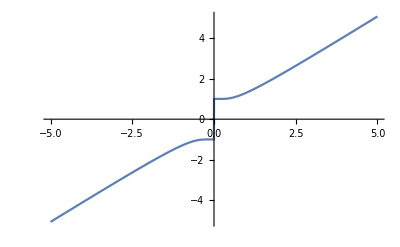

```mathematica
Plot[Coth[1/x],{x,-5,5}]
```

```mathematica
resultBroadCollins/.xi2->xi1
%//FullSimplify
Integrate[%,{xi,0,xi1}]
%//FullSimplify
Integrate[%,{tau,0,tau}]
Series[%,{xi1,0,1}]//Normal
Series[%,{eps,0,1}]
```

(log(ξ_1) τ^(-2 ϵ-1))/(ξ_1^2-1)

(log(ξ_1) τ^(-2 ϵ-1))/(ξ_1^2-1)

(ξ_1 log(ξ_1) τ^(-2 ϵ-1))/(ξ_1^2-1)

(ξ_1 log(ξ_1) τ^(-2 ϵ-1))/(ξ_1^2-1)

Integrate::idiv: Integral of TraditionalForm`Integrate`ImproperDump`newx$301421^-2\ ϵ - 1 does not converge on TraditionalForm`{0, τ}.

∫_0^τ (ξ_1 log(ξ_1) τ^(-2 ϵ-1))/(ξ_1^2-1)ⅆτ

Integrate::idiv: Integral of TraditionalForm`Integrate`ImproperDump`newx$301904^-2\ ϵ - 1 does not converge on TraditionalForm`{0, τ}.

Integrate::idiv: Integral of TraditionalForm`Integrate`ImproperDump`newx$302367^-2\ ϵ - 1 does not converge on TraditionalForm`{0, τ}.

-ξ_1 log(ξ_1) (∫_0^τ τ^(-2 ϵ-1)ⅆτ)

Integrate::idiv: Integral of \!
\(TraditionalForm\`\(1\/Integrate`ImproperDump`newx$303153 - 
     \(2\ ϵ\ \(\(log(Integrate`ImproperDump`newx$303153)\)\)\)\/Integrate`ImproperDump`newx$303153\)\)
 does not converge on TraditionalForm`{0, τ}.

-ξ_1 log(ξ_1) (∫_0^τ τ^(-2 ϵ-1)ⅆτ)

```mathematica
sigma=DiracDelta[tau-delta]+alphaMS*4*Pi*Cf*(muMS^2*Exp[EulerGamma]/(4*Pi*Q^2))^eps*2*Pi^((D-2)/2)*resultBroadCollins/(Gamma[(D-2)/2]*(2*Pi)^(D-1))
%/.D->4-2*eps
%/. tau^(-1-2*eps)->-DiracDelta[tau-delta]/(2*eps)+PlusDistribution[HeavisideTheta[tau]/tau]-2*eps*PlusDistribution[HeavisideTheta[tau]*Log[tau]/tau]

SeriesCoefficient[%,{eps,0,0}]


%//replSingVarPlus
Integrate[%,{tau,0,tau}]

FullSimplify[%,Assumptions->delta>0&&tau>beta>0&&tau>delta]
Integrate[%/.xi2->xi1,{xi1,0,xi1}]
%-xi1
Series[%,{xi1,0,1}]//Normal
```

(ⅇ^(ℽ ϵ) C_F 2^(-D-2 ϵ+4) π^((D-2)/2-D-ϵ+2) α_OverBar[MS] (μ_OverBar[MS]^2/Q^2)^ϵ ((log(((ξ_1+1) ξ_2)/(ξ_2+1)) τ^(-2 ϵ-1))/(2 (ξ_1 ξ_2-1))+(log((ξ_1 (ξ_2+1))/(ξ_1+1)) τ^(-2 ϵ-1))/(2 (ξ_1 ξ_2-1))))/((D-2)/2)+τ-δ

(ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) C_F α_OverBar[MS] (μ_OverBar[MS]^2/Q^2)^ϵ ((log(((ξ_1+1) ξ_2)/(ξ_2+1)) τ^(-2 ϵ-1))/(2 (ξ_1 ξ_2-1))+(log((ξ_1 (ξ_2+1))/(ξ_1+1)) τ^(-2 ϵ-1))/(2 (ξ_1 ξ_2-1))))/(1/2 (2-2 ϵ))+τ-δ

(ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) C_F α_OverBar[MS] (μ_OverBar[MS]^2/Q^2)^ϵ ((log(((ξ_1+1) ξ_2)/(ξ_2+1)) (-(τ-δ)/(2 ϵ)+(τ/τ)_+-2 ϵ ((τ log(τ))/τ)_+))/(2 (ξ_1 ξ_2-1))+(log((ξ_1 (ξ_2+1))/(ξ_1+1)) (-(τ-δ)/(2 ϵ)+(τ/τ)_+-2 ϵ ((τ log(τ))/τ)_+))/(2 (ξ_1 ξ_2-1))))/(1/2 (2-2 ϵ))+τ-δ

τ-δ-(C_F α_OverBar[MS] (log(((ξ_1+1) ξ_2)/(ξ_2+1)) τ-δ log(μ_OverBar[MS]^2/Q^2)+log((ξ_1 (ξ_2+1))/(ξ_1+1)) τ-δ log(μ_OverBar[MS]^2/Q^2)-2 (τ/τ)_+ log(((ξ_1+1) ξ_2)/(ξ_2+1))-2 (τ/τ)_+ log((ξ_1 (ξ_2+1))/(ξ_1+1))))/(4 π (ξ_1 ξ_2-1))

τ-δ-(C_F α_OverBar[MS] (-2 log(((ξ_1+1) ξ_2)/(ξ_2+1)) (log(τ) τ-β+(τ-β)/τ)-2 log((ξ_1 (ξ_2+1))/(ξ_1+1)) (log(τ) τ-β+(τ-β)/τ)+log(((ξ_1+1) ξ_2)/(ξ_2+1)) τ-δ log(μ_OverBar[MS]^2/Q^2)+log((ξ_1 (ξ_2+1))/(ξ_1+1)) τ-δ log(μ_OverBar[MS]^2/Q^2)))/(4 π (ξ_1 ξ_2-1))

Piecewise[{{(δ,τ-δ (4 π (ξ_1 ξ_2-1)-C_F log(ξ_1 ξ_2) α_OverBar[MS] log(μ_OverBar[MS]^2/Q^2))+2 C_F log(ξ_1 ξ_2) α_OverBar[MS] log(τ))/(4 π (ξ_1 ξ_2-1)), δ∈ℝ∧0<Re(β)<τ∧Im(β)==0}, {0, True}}]

1-(C_F log(ξ_1 ξ_2) α_OverBar[MS] log(μ_OverBar[MS]^2/(Q^2 τ^2)))/(4 π (ξ_1 ξ_2-1))

ξ_1-(C_F α_OverBar[MS] (-6 log(ξ_1) log(ξ_1+1)-6 21-ξ_1-6 2-ξ_1+π^2) log(μ_OverBar[MS]^2/(Q^2 τ^2)))/(24 π)

-(C_F α_OverBar[MS] (-6 log(ξ_1) log(ξ_1+1)-6 21-ξ_1-6 2-ξ_1+π^2) log(μ_OverBar[MS]^2/(Q^2 τ^2)))/(24 π)

(ξ_1 C_F (log(ξ_1)-1) α_OverBar[MS] log(μ_OverBar[MS]^2/(Q^2 τ^2)))/(2 π)

#### LO Broadening with Chiu’s Rapidity Regulator -- using soft regulated wilson lines

```mathematica
(*igrand=w^4*nu^(eta1+eta2)/((km)^(1+eta1)(kp)^(1+eta2)); *) (* using collinear regulated Wilson lines *)
igrand=w^2*nu^eta/(km*kp*Abs[km-kp]^eta);  (* using soft regulated Wilson lines *)
onShellDelta=DiracDelta[kp*km-r^2]HeavisideTheta[kp]HeavisideTheta[km];

(* the measurement function when k is in the positive hemisphere *)
measurementDelta1=Inactive[DiracDelta][tau-kp^(1-a/2)km^(a/2)]/.a->1;
Print["Total integrand 1 is:  ", HeavisideTheta[km-kp]igrand*onShellDelta*measurementDelta1];
preMeasure1=Integrate[ HeavisideTheta[km-kp]igrand*onShellDelta*measurementDelta1,{kp,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure1//Activate];
afterMeasure1=Integrate[FullSimplify[Activate[r^(D-3)preMeasure1]]//piecewiseToBoole,{r,0,Infinity}];
afterMeasure1=afterMeasure1/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure1];
afterfinal1=Integrate[afterMeasure1,{km,0,Infinity}];
afterfinal1=Quiet[%/.D->4-2*eps//FullSimplify][[1,1,1]]


(* the measurement function when k is in the positive hemisphere *)
measurementDelta1=Inactive[DiracDelta][tau-km^(1-a/2)kp^(a/2)]/.a->1;
Print["Total integrand 2 is:  ", HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1];
preMeasure2=Integrate[ HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1,{km,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure2//Activate];
afterMeasure2=Integrate[FullSimplify[Activate[r^(D-3)preMeasure2]]//piecewiseToBoole,{r,0,Infinity}];
afterMeasure2=afterMeasure2/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure2];
afterfinal2=Integrate[afterMeasure2,{kp,0,Infinity}];
afterfinal2=Quiet[%/.D->4-2*eps//FullSimplify][[1,1,1]]

resultChiu=afterfinal1+afterfinal2
```

Total integrand 1 is:  (w^2 ν^η Abs[k^--k^+]^-η r^2-k^+ k^- k^+ k^- k^--k^+ δ[τ-√(k^+) √(k^-)])/(k^+ k^-)

After on-shell condition:  Piecewise[{{(r^(D-5) w^2 ν^η τ-r (k^-/((k^-)^2-r^2))^η)/k^-, r<k^-}, {0, True}}]

After measurement:  w^2 ν^η τ^(D-5) Boole[τ<k^-] (k^-)^(η-1) (1/((k^-)^2-τ^2))^η

(w^2 (1/ν)^-η -η η/2 τ^(-η-2 ϵ-1))/(-η/2)

Total integrand 2 is:  (w^2 ν^η Abs[k^--k^+]^-η r^2-k^+ k^- k^+ k^+-k^- k^- δ[τ-√(k^+) √(k^-)])/(k^+ k^-)

After on-shell condition:  Piecewise[{{(r^(D-5) w^2 ν^η τ-r (k^+/((k^+)^2-r^2))^η)/k^+, r<k^+}, {0, True}}]

After measurement:  w^2 ν^η τ^(D-5) Boole[τ<k^+] (k^+)^(η-1) (1/((k^+)^2-τ^2))^η

(w^2 (1/ν)^-η -η η/2 τ^(-η-2 ϵ-1))/(-η/2)

(2 w^2 (1/ν)^-η -η η/2 τ^(-η-2 ϵ-1))/(-η/2)

```mathematica
sigmaChiuInit=DiracDelta[tau-delta]+2(* this two is for both diagrams*)*alphaMS*4*Pi*Cf*(muMS^2*Exp[EulerGamma]/(4*Pi*Q^2))^eps*Q^(-eta)2*Pi^((D-2)/2)*resultChiu/(Gamma[(D-2)/2]*(2*Pi)^(D-1));
%/.D->4-2*eps/.(tau/nu)^(-eta)->tau^(-eta)*nu^eta;
%/. tau^(-1+a_):> -DiracDelta[tau-delta]/(-a)+PlusDistribution[HeavisideTheta[tau]/tau]+a*PlusDistribution[HeavisideTheta[tau]*Log[tau]/tau];

(* take care of eta *)
sigmaChiu=Series[%,{eta,0,0}]//Normal//FullSimplify
diffCTermChiu=(Series[sigmaChiu+1/eta,{eta,0,-1}]-1/eta)//Normal
Print[diffCTermChiu];

(* take care of epsilon *)
sigmaChiu2=sigmaChiu-diffCTermChiu//FullSimplify
diffCTermChiu+=(Series[sigmaChiu2,{eps,0,-1}]//Normal)
Print[diffCTermChiu];

diffSoftChiu=sigmaChiu-diffCTermChiu//FullSimplify
diffCTermChiu+=DiracDelta[tau-delta]

diffSoftChiu=Series[diffSoftChiu/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//FullSimplify,{eps,0,0}]//Normal
Integrate[diffSoftChiu,{tau,0,tau+delta},Assumptions->beta>0&&delta>0&&nu>0]
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify
Series[%,{alphaMS,0,1}]//Normal
intSoftChiu=FullSimplify[%,Assumptions->muMS>0&&Q>0&&tau>0]/.w->1

FullSimplify[intSoftChiu,Assumptions->Q>0&&tau>0&&muMS>0&&nu>0]
%/.Log[Q*tau*muMS/nu^2]->2Log[Q*tau/nu]+Log[muMS/(tau*Q)]//Expand
intSoftChiu=%/.Log[Q*tau/muMS]->-Log[muMS/(Q*tau)]
```

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(4 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ ((τ-δ)/(4 ϵ^2)-log(Q/ν) (-(τ-δ)/(2 ϵ)+(1/τ)_+-2 ϵ ((log(τ))/τ)_+)-((log(τ))/τ)_+))/(π 1-ϵ)+τ-δ

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)

(4 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ ((τ-δ)/(4 ϵ^2)-log(Q/ν) (-(τ-δ)/(2 ϵ)+(1/τ)_+-2 ϵ ((log(τ))/τ)_+)-((log(τ))/τ)_+))/(π 1-ϵ)+τ-δ

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)

(4 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ ((τ-δ)/(4 ϵ^2)-log(Q/ν) (-(τ-δ)/(2 ϵ)+(1/τ)_+-2 ϵ ((log(τ))/τ)_+)-((log(τ))/τ)_+))/(π 1-ϵ)-(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)-(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)+τ-δ

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)+τ-δ

τ-δ-(w^2 C_F α_OverBar[MS] (24 τ log^2(τ) τ-β+π^2 τ τ-δ-24 τ τ-δ log(μ_OverBar[MS]^2) log(Q/ν)+24 τ log(Q) τ-δ log(μ_OverBar[MS]^2)-6 τ τ-δ log^2(μ_OverBar[MS]^2)+48 τ log(τ) τ-β log(Q/ν)+48 τ log(Q) τ-δ log(Q/ν)-24 τ log^2(Q) τ-δ+48 log(τ) τ-β+48 τ-β log(Q/ν)))/(12 π τ)

Piecewise[{{(τ (48 w^2 C_F log(ν) α_OverBar[MS] log(Q)-24 w^2 C_F α_OverBar[MS] log^2(Q)-24 w^2 C_F log(ν) α_OverBar[MS] log(μ_OverBar[MS]^2)+6 w^2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)+π (12-π w^2 C_F α_OverBar[MS]))-24 w^2 C_F α_OverBar[MS] (log^2(δ+τ)+2 log(Q/ν) log((δ+τ)/β)+2 log(β) log(Q/ν)))/(12 π), β<δ+τ}, {0, True}}]

(6 w^2 C_F α_OverBar[MS] (log(μ_OverBar[MS]^2/Q^2) (-4 log(ν)+log(μ_OverBar[MS]^2)+2 log(Q))-4 log(τ) (2 log(Q/ν)+log(τ)))+π (12-π w^2 C_F α_OverBar[MS]))/(12 π)

(α_OverBar[MS] (6 w^2 C_F (log(μ_OverBar[MS]^2/Q^2) (-4 log(ν)+log(μ_OverBar[MS]^2)+2 log(Q))-4 log(τ) (2 log(Q/ν)+log(τ)))-π^2 w^2 C_F))/(12 π)+1

1-(C_F α_OverBar[MS] (-24 log(μ_OverBar[MS]/Q) (log(Q μ_OverBar[MS])-2 log(ν))+24 log(τ) (2 log(Q/ν)+log(τ))+π^2))/(12 π)

-1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2))/π+1

-1/12 π C_F α_OverBar[MS]-(4 C_F α_OverBar[MS] log((Q τ)/ν) log((Q τ)/μ_OverBar[MS]))/π-(2 C_F α_OverBar[MS] log(μ_OverBar[MS]/(Q τ)) log((Q τ)/μ_OverBar[MS]))/π+1

-1/12 π C_F α_OverBar[MS]+(4 C_F α_OverBar[MS] log((Q τ)/ν) log(μ_OverBar[MS]/(Q τ)))/π+(2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]/(Q τ)))/π+1

```mathematica
diffCTermChiu
```

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)+τ-δ

```mathematica
diffSoftChiu/.delta->0/.w->1
FullSimplify[%,Assumptions->muMS>0&&Q>0]
SeriesCoefficient[%,{DiracDelta[_],0,1}]
FullSimplify[%,Assumptions->muMS>0&&Q>0&&nu>0]
%/.Log[Q*muMS/nu^2]->Log[muMS/Q]-Log[nu^2/Q^2]/.Log[muMS/Q]->Log[muMS^2/Q^2]/2
%//Expand
```

τ-(C_F α_OverBar[MS] (24 τ log^2(τ) τ-β-24 τ τ log(μ_OverBar[MS]^2) log(Q/ν)+24 τ τ log(Q) log(μ_OverBar[MS]^2)-6 τ τ log^2(μ_OverBar[MS]^2)+48 τ log(τ) τ-β log(Q/ν)+48 τ τ log(Q) log(Q/ν)-24 τ τ log^2(Q)+π^2 τ τ+48 log(τ) τ-β+48 τ-β log(Q/ν)))/(12 π τ)

τ-(C_F α_OverBar[MS] (24 τ log^2(τ) τ-β+48 τ log(τ) τ-β log(Q/ν)+48 τ-β (log(Q/ν)+log(τ))))/(12 π τ)

(-2 C_F α_OverBar[MS] log^2(τ)-4 C_F α_OverBar[MS] log(τ) log(Q/ν)+π)/π

1-(2 C_F α_OverBar[MS] log(τ) log((Q^2 τ)/ν^2))/π

1-(2 C_F α_OverBar[MS] log(τ) log((Q^2 τ)/ν^2))/π

1-(2 C_F α_OverBar[MS] log(τ) log((Q^2 τ)/ν^2))/π

```mathematica
diffSoftChiu/.delta->0/.w->1
FullSimplify[%,Assumptions->muMS>0&&Q>0]
SeriesCoefficient[%,{DiracDelta[_],0,0}]
```

τ-(C_F α_OverBar[MS] (24 τ log^2(τ) τ-β-24 τ τ log(μ_OverBar[MS]^2) log(Q/ν)+24 τ τ log(Q) log(μ_OverBar[MS]^2)-6 τ τ log^2(μ_OverBar[MS]^2)+48 τ log(τ) τ-β log(Q/ν)+48 τ τ log(Q) log(Q/ν)-24 τ τ log^2(Q)+π^2 τ τ+48 log(τ) τ-β+48 τ-β log(Q/ν)))/(12 π τ)

τ-(C_F α_OverBar[MS] (24 τ log^2(τ) τ-β+48 τ log(τ) τ-β log(Q/ν)+48 τ-β (log(Q/ν)+log(τ))))/(12 π τ)

-(4 C_F α_OverBar[MS] τ-β log((Q τ)/ν))/(π τ)

```mathematica
intSoftChiu//Expand
FullSimplify[%,Assumptions->Q>0&&tau>0&&muMS>0&&nu>0]
hardFunc*(%+alphaMS*Cf*g/(2*Pi))
Series[%,{alphaMS,0,1}]//Normal
Solve[%==answerBroad,g]//Flatten
gFuncChiu=g/.%
```

-1/12 π C_F α_OverBar[MS]+(4 C_F α_OverBar[MS] log((Q τ)/ν) log(μ_OverBar[MS]/(Q τ)))/π+(2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]/(Q τ)))/π+1

-1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2))/π+1

((α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)+1) ((g C_F α_OverBar[MS])/(2 π)-1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2))/π+1)

(α_OverBar[MS] (g C_F-C_F log^2(μ_OverBar[MS]^2/Q^2)-3 C_F log(μ_OverBar[MS]^2/Q^2)-4 C_F log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-8 C_F+π^2 C_F))/(2 π)+1

{g→log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-4 log^2(τ)-6 log(τ)+1}

log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-4 log^2(τ)-6 log(τ)+1

```mathematica
gFuncChiu


(* PRETTY GOOD *)
%/.Log[Q*tau*muMS/nu^2]->Log[muMS/Q]-2Log[nu/nuJ]//Expand
%/.Log[Q*tau/muMS]->-Log[muMS/(Q*tau)]

%/.Log[muMS/Q]Log[muMS/(tau*Q)]->Log[muMS/Q](Log[muMS/Q]-Log[tau])//Expand
%/.Log[muMS^2/Q^2]->2*Log[muMS/Q]

rah=%/.tau->muS/Q

rah1=SeriesCoefficient[rah,{Log[nu/nuJ],0,1}]/.Log[muMS/muS]->RS
SeriesCoefficient[rah,{Log[nu/nuJ],0,0}]-1//expLogs//Expand
rahrah=%/. 4->xx/.-4->-xx/. 6->xx+yy/.-6->-xx-yy
rah2=(SeriesCoefficient[rahrah,{xx,0,1}]//FullSimplify)/.Log[muMS]-Log[muS]->RS
rah3=(SeriesCoefficient[rahrah,{yy,0,1}]//FullSimplify)/.Log[muMS]-Log[muS]->RS

1+rah1*Log[nu/nuJ]+4*rah2+2rah3/.Log[nu/nuJ]->Log[nu^2/nuJ^2]/2
%//FullSimplify
%/.Log[nu^2/(Q*nuJ^2)]+Log[muS]->Log[nu^2/Q^2]
matchCSChiu=1+alphaMS*Cf*%/(2*Pi)/.RS->Log[muMS^2/(tau^2*Q^2)]/2

(*

(*PRETTY MEH *)
%/.Log[Q*tau*muMS/nu^2]->2Log[nuS/nu]+Log[muMS/Q]-Log[tau]//Expand
%/.Log[Q*tau/muMS]->-Log[muMS/(Q*tau)]

%/.Log[muMS/Q]Log[muMS/(tau*Q)]->Log[muMS/Q](Log[muMS/Q]-Log[tau])//Expand
%/.Log[muMS^2/Q^2]->2*Log[muMS/Q]

%/.Log[muMS^2/Q^2]->2Log[muMS/Q]/.Log[muMS/(tau*Q)]->Log[muMS/Q]-Log[tau]//Expand
Collect2[%,Log[tau]]

%/. tau->muS^2/muJ^2
%//expLogs//Expand
SeriesCoefficient[%,{Log[Q],0,0}]
*)
```

log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-4 log^2(τ)-6 log(τ)+1

-8 log(ν/ν_J) log((Q τ)/μ_OverBar[MS])+log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log(μ_OverBar[MS]/Q) log((Q τ)/μ_OverBar[MS])-4 log^2(τ)-6 log(τ)+1

8 log(ν/ν_J) log(μ_OverBar[MS]/(Q τ))+log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)-4 log(μ_OverBar[MS]/Q) log(μ_OverBar[MS]/(Q τ))-4 log^2(τ)-6 log(τ)+1

8 log(ν/ν_J) log(μ_OverBar[MS]/(Q τ))+log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log(τ) log(μ_OverBar[MS]/Q)-4 log^2(μ_OverBar[MS]/Q)-4 log^2(τ)-6 log(τ)+1

8 log(ν/ν_J) log(μ_OverBar[MS]/(Q τ))+4 log(τ) log(μ_OverBar[MS]/Q)+6 log(μ_OverBar[MS]/Q)-4 log^2(τ)-6 log(τ)+1

8 log(ν/ν_J) log(μ_OverBar[MS]/μ_S)+4 log(μ_OverBar[MS]/Q) log(μ_S/Q)+6 log(μ_OverBar[MS]/Q)-4 log^2(μ_S/Q)-6 log(μ_S/Q)+1

8 RS

-4 log(Q) log(μ_OverBar[MS])+4 log(μ_OverBar[MS]) log(μ_S)+6 log(μ_OverBar[MS])+4 log(Q) log(μ_S)-4 log^2(μ_S)-6 log(μ_S)

-xx log(Q) log(μ_OverBar[MS])+xx log(μ_OverBar[MS]) log(μ_S)+(xx+yy) log(μ_OverBar[MS])+xx log(Q) log(μ_S)+(-xx-yy) log(μ_S)-xx log^2(μ_S)

RS (-log(Q)+log(μ_S)+1)

RS

4 RS log(ν^2/ν_J^2)+4 RS (-log(Q)+log(μ_S)+1)+2 RS+1

4 RS (log(ν^2/(Q ν_J^2))+log(μ_S))+6 RS+1

4 RS log(ν^2/Q^2)+6 RS+1

(C_F α_OverBar[MS] (2 log(ν^2/Q^2) log(μ_OverBar[MS]^2/(Q^2 τ^2))+3 log(μ_OverBar[MS]^2/(Q^2 τ^2))+1))/(2 π)+1

```mathematica
diffSoftResult
```

diffSoftResult

```mathematica
(* check *) 
igrandCheck=hardFunc*(matchCSChiu/.tau->tprime)*(diffSoftChiu/.tau->tau-tprime)
Series[%,{alphaMS,0,1}]//Normal
myBroadeningRate=Integrate[%,{tprime,0,tau},Assumptions->(delta+tau)>beta>0&&tau>delta>0&&t>tau>0&&tau>beta]

myBroadeningRate/.t->tau+delta/.w->1

FullSimplify[%,Assumptions->delta>0&&beta>0&&(delta+tau)>beta]
Limit[%,delta->0]
%//expLogs//Expand
myBroadeningRate=Collect2[%,alphaMS]
```

((α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)+1) ((C_F α_OverBar[MS] (2 log(ν^2/Q^2) log(μ_OverBar[MS]^2/(Q^2 tprime^2))+3 log(μ_OverBar[MS]^2/(Q^2 tprime^2))+1))/(2 π)+1) (tprime+δ-τ-1/(12 π (τ-tprime))w^2 C_F α_OverBar[MS] (-24 (τ-tprime) log(μ_OverBar[MS]^2) log(Q/ν) tprime+δ-τ+24 log(Q) (τ-tprime) log(μ_OverBar[MS]^2) tprime+δ-τ-6 (τ-tprime) log^2(μ_OverBar[MS]^2) tprime+δ-τ+48 (τ-tprime) log(Q/ν) log(τ-tprime) tprime+β-τ+48 log(Q) (τ-tprime) log(Q/ν) tprime+δ-τ-24 log^2(Q) (τ-tprime) tprime+δ-τ+24 (τ-tprime) log^2(τ-tprime) tprime+β-τ+π^2 (τ-tprime) tprime+δ-τ+48 log(Q/ν) -tprime-β+τ+48 log(τ-tprime) -tprime-β+τ))

α_OverBar[MS] (tprime+δ-τ ((2 C_F log(ν^2/Q^2) log(μ_OverBar[MS]^2/(Q^2 tprime^2))+3 C_F log(μ_OverBar[MS]^2/(Q^2 tprime^2))+C_F)/(2 π)+(-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F)/(12 π))-1/(12 π (τ-tprime))w^2 C_F (-24 (τ-tprime) log(μ_OverBar[MS]^2) log(Q/ν) tprime+δ-τ+24 log(Q) (τ-tprime) log(μ_OverBar[MS]^2) tprime+δ-τ-6 (τ-tprime) log^2(μ_OverBar[MS]^2) tprime+δ-τ+48 (τ-tprime) log(Q/ν) log(τ-tprime) tprime+β-τ+48 log(Q) (τ-tprime) log(Q/ν) tprime+δ-τ-24 log^2(Q) (τ-tprime) tprime+δ-τ+24 (τ-tprime) log^2(τ-tprime) tprime+β-τ+π^2 (τ-tprime) tprime+δ-τ+48 log(Q/ν) -tprime-β+τ+48 log(τ-tprime) -tprime-β+τ))+tprime+δ-τ

-1/(12 π)(36 C_F α_OverBar[MS] log(τ-δ)+42 C_F α_OverBar[MS]-7 π^2 C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(τ-δ) log(ν^2/Q^2)-12 C_F α_OverBar[MS] log(ν^2/Q^2) log(μ_OverBar[MS]^2/Q^2)+6 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2/Q^2)+24 w^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2) (log(Q)-log(Q/ν))+48 w^2 C_F α_OverBar[MS] log(τ/β) log(Q/ν)+48 w^2 log(β) C_F α_OverBar[MS] log(Q/ν)+48 w^2 C_F α_OverBar[MS] log(Q) log(Q/ν)-24 w^2 C_F α_OverBar[MS] log^2(Q)-6 w^2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)+24 w^2 C_F α_OverBar[MS] log^2(τ)+π^2 w^2 C_F α_OverBar[MS]-12 π)

-(36 C_F α_OverBar[MS] log(τ-δ)+24 C_F α_OverBar[MS] log^2(τ)+42 C_F α_OverBar[MS]-6 π^2 C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(τ-δ) log(ν^2/Q^2)-12 C_F α_OverBar[MS] log(ν^2/Q^2) log(μ_OverBar[MS]^2/Q^2)+6 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2/Q^2)+48 C_F α_OverBar[MS] log(τ/β) log(Q/ν)+48 log(β) C_F α_OverBar[MS] log(Q/ν)+48 C_F α_OverBar[MS] log(Q) log(Q/ν)-24 C_F α_OverBar[MS] log^2(Q)+24 C_F α_OverBar[MS] log(μ_OverBar[MS]^2) (log(Q)-log(Q/ν))-6 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)-12 π)/(12 π)

((π^2-7) C_F α_OverBar[MS]+C_F α_OverBar[MS] (2 log(ν^2/Q^2) log(μ_OverBar[MS]^2/Q^2)-log^2(μ_OverBar[MS]^2/Q^2)+(log(μ_OverBar[MS]^2)-2 (log(Q)+log(τ))) (log(μ_OverBar[MS]^2)+4 log(Q/ν)-2 log(Q)+2 log(τ))-2 log(τ-δ) (2 log(ν^2/Q^2)+3))+2 π)/(2 π)

-(4 C_F log(ν^2) α_OverBar[MS] log(τ)+8 C_F log(1/ν) α_OverBar[MS] log(τ)+4 C_F α_OverBar[MS] log^2(τ)+6 C_F α_OverBar[MS] log(τ)+7 C_F α_OverBar[MS]-π^2 C_F α_OverBar[MS]+4 C_F (log(ν^2)+2 log(1/ν)) α_OverBar[MS] log(Q)-2 C_F (log(ν^2)+2 log(1/ν)) α_OverBar[MS] log(μ_OverBar[MS]^2)-2 π)/(2 π)

-(2 C_F α_OverBar[MS] log^2(τ))/π-(3 C_F α_OverBar[MS] log(τ))/π+1/2 π C_F α_OverBar[MS]-(7 C_F α_OverBar[MS])/(2 π)+1

(C_F α_OverBar[MS] (-4 log^2(τ)-6 log(τ)+π^2-7))/(2 π)+1

```mathematica
answerBroad
```

(C_F α_OverBar[MS] (-8 log^2(τ)-12 log(τ)+2 π^2-14))/(4 π)+1

```mathematica
hardFunc
```

(α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)+1

```mathematica
answerBroad-hardFunc+(hardFunc/.Q->nu)
%//expLogs//Expand

Collect2[%,Log[Q],Log[nu]]
%/.Log[muMS]->-LS/2+Log[tau*Q]//expLogs//Expand
%/.Log[Q]->LNS/2+Log[nu]-Log[tau]//Expand
%//FullSimplify
Collect2[%,LS]
%/.LNS-2Log[tau]->LQ
%//FullSimplify
%/.Pi^2->6zeta2/.alphaMS->2*Pi*alphabar/Cf//Simplify
%/.LNS->Log[Q^2*tau^2/nu^2]/.LQ->Log[Q^2/muMS^2]/.LS->Log[tau^2*Q^2/muMS^2]
%/.nu->Q//expLogs//Expand
```

(C_F α_OverBar[MS] (-8 log^2(τ)-12 log(τ)+2 π^2-14))/(4 π)-(α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)+(α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/ν^2)-18 C_F log(μ_OverBar[MS]^2/ν^2)-48 C_F+7 π^2 C_F))/(12 π)+1

-(2 C_F log^2(ν) α_OverBar[MS])/π+(3 C_F log(ν) α_OverBar[MS])/π-(2 C_F α_OverBar[MS] log^2(τ))/π-(3 C_F α_OverBar[MS] log(τ))/π+1/2 π C_F α_OverBar[MS]-(7 C_F α_OverBar[MS])/(2 π)+(2 C_F α_OverBar[MS] log^2(Q))/π-(3 C_F α_OverBar[MS] log(Q))/π-(4 C_F α_OverBar[MS] log(Q) log(μ_OverBar[MS]))/π+(4 C_F log(ν) α_OverBar[MS] log(μ_OverBar[MS]))/π+1

-(2 C_F log^2(ν) α_OverBar[MS])/π+(-4 C_F α_OverBar[MS] log^2(τ)-6 C_F α_OverBar[MS] log(τ)-7 C_F α_OverBar[MS]+π^2 C_F α_OverBar[MS]+2 π)/(2 π)+(2 C_F α_OverBar[MS] log^2(Q))/π-(C_F α_OverBar[MS] log(Q) (4 log(μ_OverBar[MS])+3))/π+(C_F log(ν) α_OverBar[MS] (4 log(μ_OverBar[MS])+3))/π

-(2 LS C_F log(ν) α_OverBar[MS])/π+(2 LS C_F α_OverBar[MS] log(Q))/π+(4 C_F log(ν) α_OverBar[MS] log(τ))/π-(2 C_F log^2(ν) α_OverBar[MS])/π+(3 C_F log(ν) α_OverBar[MS])/π-(2 C_F α_OverBar[MS] log^2(τ))/π-(3 C_F α_OverBar[MS] log(τ))/π+1/2 π C_F α_OverBar[MS]-(7 C_F α_OverBar[MS])/(2 π)+(4 C_F log(ν) α_OverBar[MS] log(Q))/π-(4 C_F α_OverBar[MS] log(Q) log(τ))/π-(2 C_F α_OverBar[MS] log^2(Q))/π-(3 C_F α_OverBar[MS] log(Q))/π+1

-(LNS^2 C_F α_OverBar[MS])/(2 π)+(LNS LS C_F α_OverBar[MS])/π-(3 LNS C_F α_OverBar[MS])/(2 π)-(2 LS C_F α_OverBar[MS] log(τ))/π+1/2 π C_F α_OverBar[MS]-(7 C_F α_OverBar[MS])/(2 π)+1

(C_F (-LNS (LNS-2 LS+3)+π^2-7) α_OverBar[MS]-4 LS C_F α_OverBar[MS] log(τ)+2 π)/(2 π)

(LNS^2 C_F (-α_OverBar[MS])-3 LNS C_F α_OverBar[MS]-7 C_F α_OverBar[MS]+π^2 C_F α_OverBar[MS]+2 π)/(2 π)+(LS C_F α_OverBar[MS] (LNS-2 log(τ)))/π

(LNS^2 C_F (-α_OverBar[MS])-3 LNS C_F α_OverBar[MS]-7 C_F α_OverBar[MS]+π^2 C_F α_OverBar[MS]+2 π)/(2 π)+(LQ LS C_F α_OverBar[MS])/π

(C_F α_OverBar[MS] (-LNS (LNS+3)+2 LQ LS+π^2-7)+2 π)/(2 π)

1-ᾱ (-6 ζ_2+LNS^2+3 LNS-2 LQ LS+7)

1-ᾱ (-6 ζ_2-2 log(Q^2/μ_OverBar[MS]^2) log((Q^2 τ^2)/μ_OverBar[MS]^2)+log^2((Q^2 τ^2)/ν^2)+3 log((Q^2 τ^2)/ν^2)+7)

6 ζ_2 ᾱ-4 ᾱ log^2(τ)-6 ᾱ log(τ)-7 ᾱ-16 ᾱ log(Q) log(μ_OverBar[MS])-8 ᾱ log(τ) log(μ_OverBar[MS])+8 ᾱ log^2(μ_OverBar[MS])+8 ᾱ log(Q) log(τ)+8 ᾱ log^2(Q)+1

```mathematica
answerBroad-hardFunc//expLogs//Expand
%/.Log[muMS]->-LS/2+Log[Q*tau]//expLogs//Expand
%/.Log[tau]->(LS-LQ)/2//Expand
```

-(2 C_F α_OverBar[MS] log^2(τ))/π-(3 C_F α_OverBar[MS] log(τ))/π-1/12 π C_F α_OverBar[MS]+(C_F α_OverBar[MS])/(2 π)+(2 C_F α_OverBar[MS] log^2(Q))/π-(3 C_F α_OverBar[MS] log(Q))/π-(4 C_F α_OverBar[MS] log(Q) log(μ_OverBar[MS]))/π+(2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]))/π+(3 C_F α_OverBar[MS] log(μ_OverBar[MS]))/π

(LS^2 C_F α_OverBar[MS])/(2 π)-(2 LS C_F α_OverBar[MS] log(τ))/π-(3 LS C_F α_OverBar[MS])/(2 π)-1/12 π C_F α_OverBar[MS]+(C_F α_OverBar[MS])/(2 π)

(LQ LS C_F α_OverBar[MS])/π-(LS^2 C_F α_OverBar[MS])/(2 π)-(3 LS C_F α_OverBar[MS])/(2 π)-1/12 π C_F α_OverBar[MS]+(C_F α_OverBar[MS])/(2 π)

```mathematica
hardFunc/.Log[muMS^2/Q^2]->-LQ/.Pi^2->6zeta2/.alphaMS->2*Pi*alphabar/Cf//Simplify
%/.-3LQ->-(3LQ+2LM LN)//Expand
%//Simplify
```

1-ᾱ (-7 ζ_2+LQ^2-3 LQ+8)

7 ζ_2 ᾱ-8 ᾱ+2 LM LN ᾱ+LQ^2 (-ᾱ)+3 LQ ᾱ+1

ᾱ (7 ζ_2+2 LM LN-LQ^2+3 LQ-8)+1

```mathematica
hardFunc-(hardFunc/.Q->nu)
%//expLogs//Expand
%/.Log[Q]->LR/2+Log[nu]//Expand
%/.Log[nu]->LN/2+Log[muMS]//Expand
```

(α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)-(α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/ν^2)-18 C_F log(μ_OverBar[MS]^2/ν^2)-48 C_F+7 π^2 C_F))/(12 π)

(2 C_F log^2(ν) α_OverBar[MS])/π-(3 C_F log(ν) α_OverBar[MS])/π-(2 C_F α_OverBar[MS] log^2(Q))/π+(3 C_F α_OverBar[MS] log(Q))/π+(4 C_F α_OverBar[MS] log(Q) log(μ_OverBar[MS]))/π-(4 C_F log(ν) α_OverBar[MS] log(μ_OverBar[MS]))/π

-(LR^2 C_F α_OverBar[MS])/(2 π)-(2 LR C_F log(ν) α_OverBar[MS])/π+(3 LR C_F α_OverBar[MS])/(2 π)+(2 LR C_F α_OverBar[MS] log(μ_OverBar[MS]))/π

-(LN LR C_F α_OverBar[MS])/π-(LR^2 C_F α_OverBar[MS])/(2 π)+(3 LR C_F α_OverBar[MS])/(2 π)

#### LO Broadening with Chiu’s Rapidity Regulator -- using collinear regulated Wilson lines

```mathematica
igrand=w^4*nu^(eta1+eta2)/((km)^(1+eta1)(kp)^(1+eta2));  (* using collinear regulated Wilson lines *)
(*igrand=w^2*nu^eta/(km*kp*Abs[km-kp]^eta);*)  (* using soft regulated Wilson lines *)
onShellDelta=DiracDelta[kp*km-r^2]HeavisideTheta[kp]HeavisideTheta[km];

(* the measurement function when k is in the positive hemisphere *)
measurementDelta1=Inactive[DiracDelta][tau-kp^(1-a/2)km^(a/2)]/.a->1;
Print["Total integrand 1 is:  ",(* HeavisideTheta[km-kp]*)igrand*onShellDelta*measurementDelta1];
preMeasure1=Integrate[ HeavisideTheta[km-kp]igrand*onShellDelta*measurementDelta1,{kp,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure1//Activate];
afterMeasure1=Integrate[FullSimplify[Activate[r^(D-3)preMeasure1]]//piecewiseToBoole,{r,0,Infinity}];
afterMeasure1=afterMeasure1/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure1];
afterfinal1=Integrate[afterMeasure1,{km,0,Infinity}];
afterfinal1=Quiet[%/.D->4-2*eps//FullSimplify][[1,1,1]]


(* the measurement function when k is in the positive hemisphere *)
(*measurementDelta1=Inactive[DiracDelta][tau-km^(1-a/2)kp^(a/2)]/.a->1;
Print["Total integrand 2 is:  ", HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1];
preMeasure2=Integrate[ HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1,{km,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure2//Activate];
afterMeasure2=Integrate[FullSimplify[Activate[r^(D-3)preMeasure2]]//piecewiseToBoole,{r,0,Infinity}];
afterMeasure2=afterMeasure2/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure2];
afterfinal2=Integrate[afterMeasure2,{kp,0,Infinity}];
afterfinal2=Quiet[%/.D->4-2*eps//FullSimplify][[1,1,1]]*)

resultChiu=afterfinal1+afterfinal2
```

Total integrand 1 is:  w^4 ν^(η_1+η_2) r^2-k^+ k^- k^+ k^- (k^+)^(-η_2-1) (k^-)^(-η_1-1) δ[τ-√(k^+) √(k^-)]

After on-shell condition:  r^(D-2 (η_2+1)-3) w^4 ν^(η_1+η_2) τ-r r^2/k^-,k^-,k^--r^2/k^- (k^-)^(-η_1+η_2-1)

After measurement:  Piecewise[{{w^4 ν^(η_1+η_2) τ^(D-2 η_2-5) (k^-)^(-η_1+η_2-1), τ≤k^-}, {0, True}}]

(w^4 ν^(η_1+η_2) τ^(-η_1-η_2-2 ϵ-1))/(η_1-η_2)

0

```mathematica
sigmaChiuInit=DiracDelta[tau-delta]+2(* this two is for both diagrams*)*alphaMS*4*Pi*Cf*(muMS^2*Exp[EulerGamma]/(4*Pi*Q^2))^eps*Q^(-eta)2*Pi^((D-2)/2)*resultChiu/(Gamma[(D-2)/2]*(2*Pi)^(D-1));
%/.D->4-2*eps/.(tau/nu)^(-eta)->tau^(-eta)*nu^eta;
%/. tau^(-1+a_):> -DiracDelta[tau-delta]/(-a)+PlusDistribution[HeavisideTheta[tau]/tau]+a*PlusDistribution[HeavisideTheta[tau]*Log[tau]/tau];

(* take care of eta *)
sigmaChiu=Series[%,{eta,0,0}]//Normal//FullSimplify
diffCTermChiu=(Series[sigmaChiu+1/eta,{eta,0,-1}]-1/eta)//Normal
Print[diffCTermChiu];

(* take care of epsilon *)
sigmaChiu2=sigmaChiu-diffCTermChiu//FullSimplify
diffCTermChiu+=(Series[sigmaChiu2,{eps,0,-1}]//Normal)
Print[diffCTermChiu];

diffSoftChiu=sigmaChiu-diffCTermChiu//FullSimplify
diffCTermChiu+=DiracDelta[tau-delta]

diffSoftChiu=Series[diffSoftChiu/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//FullSimplify,{eps,0,0}]//Normal
Integrate[diffSoftChiu,{tau,0,tau+delta},Assumptions->beta>0&&delta>0&&nu>0]
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify
Series[%,{alphaMS,0,1}]//Normal
intSoftChiu=FullSimplify[%,Assumptions->muMS>0&&Q>0&&tau>0]/.w->1

FullSimplify[intSoftChiu,Assumptions->Q>0&&tau>0&&muMS>0&&nu>0]
%/.Log[Q*tau*muMS/nu^2]->2Log[Q*tau/nu]+Log[muMS/(tau*Q)]//Expand
intSoftChiu=%/.Log[Q*tau/muMS]->-Log[muMS/(Q*tau)]
```

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(4 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ ((τ-δ)/(4 ϵ^2)-log(Q/ν) (-(τ-δ)/(2 ϵ)+(1/τ)_+-2 ϵ ((log(τ))/τ)_+)-((log(τ))/τ)_+))/(π 1-ϵ)+τ-δ

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)

(4 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ ((τ-δ)/(4 ϵ^2)-log(Q/ν) (-(τ-δ)/(2 ϵ)+(1/τ)_+-2 ϵ ((log(τ))/τ)_+)-((log(τ))/τ)_+))/(π 1-ϵ)+τ-δ

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)

(4 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ ((τ-δ)/(4 ϵ^2)-log(Q/ν) (-(τ-δ)/(2 ϵ)+(1/τ)_+-2 ϵ ((log(τ))/τ)_+)-((log(τ))/τ)_+))/(π 1-ϵ)-(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)-(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)+τ-δ

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)+τ-δ

τ-δ-(w^2 C_F α_OverBar[MS] (24 τ log^2(τ) τ-β+π^2 τ τ-δ-24 τ τ-δ log(μ_OverBar[MS]^2) log(Q/ν)+24 τ log(Q) τ-δ log(μ_OverBar[MS]^2)-6 τ τ-δ log^2(μ_OverBar[MS]^2)+48 τ log(τ) τ-β log(Q/ν)+48 τ log(Q) τ-δ log(Q/ν)-24 τ log^2(Q) τ-δ+48 log(τ) τ-β+48 τ-β log(Q/ν)))/(12 π τ)

Piecewise[{{(τ (48 w^2 C_F log(ν) α_OverBar[MS] log(Q)-24 w^2 C_F α_OverBar[MS] log^2(Q)-24 w^2 C_F log(ν) α_OverBar[MS] log(μ_OverBar[MS]^2)+6 w^2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)+π (12-π w^2 C_F α_OverBar[MS]))-24 w^2 C_F α_OverBar[MS] (log^2(δ+τ)+2 log(Q/ν) log((δ+τ)/β)+2 log(β) log(Q/ν)))/(12 π), β<δ+τ}, {0, True}}]

(6 w^2 C_F α_OverBar[MS] (log(μ_OverBar[MS]^2/Q^2) (-4 log(ν)+log(μ_OverBar[MS]^2)+2 log(Q))-4 log(τ) (2 log(Q/ν)+log(τ)))+π (12-π w^2 C_F α_OverBar[MS]))/(12 π)

(α_OverBar[MS] (6 w^2 C_F (log(μ_OverBar[MS]^2/Q^2) (-4 log(ν)+log(μ_OverBar[MS]^2)+2 log(Q))-4 log(τ) (2 log(Q/ν)+log(τ)))-π^2 w^2 C_F))/(12 π)+1

1-(C_F α_OverBar[MS] (-24 log(μ_OverBar[MS]/Q) (log(Q μ_OverBar[MS])-2 log(ν))+24 log(τ) (2 log(Q/ν)+log(τ))+π^2))/(12 π)

-1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2))/π+1

-1/12 π C_F α_OverBar[MS]-(4 C_F α_OverBar[MS] log((Q τ)/ν) log((Q τ)/μ_OverBar[MS]))/π-(2 C_F α_OverBar[MS] log(μ_OverBar[MS]/(Q τ)) log((Q τ)/μ_OverBar[MS]))/π+1

-1/12 π C_F α_OverBar[MS]+(4 C_F α_OverBar[MS] log((Q τ)/ν) log(μ_OverBar[MS]/(Q τ)))/π+(2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]/(Q τ)))/π+1

```mathematica
diffCTermChiu
```

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(w^2 C_F α_OverBar[MS] (τ-δ log(μ_OverBar[MS]^2)+2 τ-δ log(Q/ν)-2 log(Q) τ-δ))/(π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(π ϵ^2)+τ-δ

```mathematica
diffSoftChiu/.delta->0/.w->1
FullSimplify[%,Assumptions->muMS>0&&Q>0]
SeriesCoefficient[%,{DiracDelta[_],0,1}]
FullSimplify[%,Assumptions->muMS>0&&Q>0&&nu>0]
%/.Log[Q*muMS/nu^2]->Log[muMS/Q]-Log[nu^2/Q^2]/.Log[muMS/Q]->Log[muMS^2/Q^2]/2
%//Expand
```

τ-(C_F α_OverBar[MS] (24 τ log^2(τ) τ-β-24 τ τ log(μ_OverBar[MS]^2) log(Q/ν)+24 τ τ log(Q) log(μ_OverBar[MS]^2)-6 τ τ log^2(μ_OverBar[MS]^2)+48 τ log(τ) τ-β log(Q/ν)+48 τ τ log(Q) log(Q/ν)-24 τ τ log^2(Q)+π^2 τ τ+48 log(τ) τ-β+48 τ-β log(Q/ν)))/(12 π τ)

τ-(C_F α_OverBar[MS] (24 τ log^2(τ) τ-β+48 τ log(τ) τ-β log(Q/ν)+48 τ-β (log(Q/ν)+log(τ))))/(12 π τ)

(-2 C_F α_OverBar[MS] log^2(τ)-4 C_F α_OverBar[MS] log(τ) log(Q/ν)+π)/π

1-(2 C_F α_OverBar[MS] log(τ) log((Q^2 τ)/ν^2))/π

1-(2 C_F α_OverBar[MS] log(τ) log((Q^2 τ)/ν^2))/π

1-(2 C_F α_OverBar[MS] log(τ) log((Q^2 τ)/ν^2))/π

```mathematica
diffSoftChiu/.delta->0/.w->1
FullSimplify[%,Assumptions->muMS>0&&Q>0]
SeriesCoefficient[%,{DiracDelta[_],0,0}]
```

τ-(C_F α_OverBar[MS] (24 τ log^2(τ) τ-β-24 τ τ log(μ_OverBar[MS]^2) log(Q/ν)+24 τ τ log(Q) log(μ_OverBar[MS]^2)-6 τ τ log^2(μ_OverBar[MS]^2)+48 τ log(τ) τ-β log(Q/ν)+48 τ τ log(Q) log(Q/ν)-24 τ τ log^2(Q)+π^2 τ τ+48 log(τ) τ-β+48 τ-β log(Q/ν)))/(12 π τ)

τ-(C_F α_OverBar[MS] (24 τ log^2(τ) τ-β+48 τ log(τ) τ-β log(Q/ν)+48 τ-β (log(Q/ν)+log(τ))))/(12 π τ)

-(4 C_F α_OverBar[MS] τ-β log((Q τ)/ν))/(π τ)

```mathematica
intSoftChiu//Expand
FullSimplify[%,Assumptions->Q>0&&tau>0&&muMS>0&&nu>0]
hardFunc*(%+alphaMS*Cf*g/(2*Pi))
Series[%,{alphaMS,0,1}]//Normal
Solve[%==answerBroad,g]//Flatten
gFuncChiu=g/.%
```

-1/12 π C_F α_OverBar[MS]+(4 C_F α_OverBar[MS] log((Q τ)/ν) log(μ_OverBar[MS]/(Q τ)))/π+(2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]/(Q τ)))/π+1

-1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2))/π+1

((α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)+1) ((g C_F α_OverBar[MS])/(2 π)-1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2))/π+1)

(α_OverBar[MS] (g C_F-C_F log^2(μ_OverBar[MS]^2/Q^2)-3 C_F log(μ_OverBar[MS]^2/Q^2)-4 C_F log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-8 C_F+π^2 C_F))/(2 π)+1

{g→log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-4 log^2(τ)-6 log(τ)+1}

log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-4 log^2(τ)-6 log(τ)+1

```mathematica
gFuncChiu


(* PRETTY GOOD *)
%/.Log[Q*tau*muMS/nu^2]->Log[muMS/Q]-2Log[nu/nuJ]//Expand
%/.Log[Q*tau/muMS]->-Log[muMS/(Q*tau)]

%/.Log[muMS/Q]Log[muMS/(tau*Q)]->Log[muMS/Q](Log[muMS/Q]-Log[tau])//Expand
%/.Log[muMS^2/Q^2]->2*Log[muMS/Q]

rah=%/.tau->muS/Q

rah1=SeriesCoefficient[rah,{Log[nu/nuJ],0,1}]/.Log[muMS/muS]->RS
SeriesCoefficient[rah,{Log[nu/nuJ],0,0}]-1//expLogs//Expand
rahrah=%/. 4->xx/.-4->-xx/. 6->xx+yy/.-6->-xx-yy
rah2=(SeriesCoefficient[rahrah,{xx,0,1}]//FullSimplify)/.Log[muMS]-Log[muS]->RS
rah3=(SeriesCoefficient[rahrah,{yy,0,1}]//FullSimplify)/.Log[muMS]-Log[muS]->RS

1+rah1*Log[nu/nuJ]+4*rah2+2rah3/.Log[nu/nuJ]->Log[nu^2/nuJ^2]/2
%//FullSimplify
%/.Log[nu^2/(Q*nuJ^2)]+Log[muS]->Log[nu^2/Q^2]
matchCSChiu=1+alphaMS*Cf*%/(2*Pi)/.RS->Log[muMS^2/(tau^2*Q^2)]/2

(*

(*PRETTY MEH *)
%/.Log[Q*tau*muMS/nu^2]->2Log[nuS/nu]+Log[muMS/Q]-Log[tau]//Expand
%/.Log[Q*tau/muMS]->-Log[muMS/(Q*tau)]

%/.Log[muMS/Q]Log[muMS/(tau*Q)]->Log[muMS/Q](Log[muMS/Q]-Log[tau])//Expand
%/.Log[muMS^2/Q^2]->2*Log[muMS/Q]

%/.Log[muMS^2/Q^2]->2Log[muMS/Q]/.Log[muMS/(tau*Q)]->Log[muMS/Q]-Log[tau]//Expand
Collect2[%,Log[tau]]

%/. tau->muS^2/muJ^2
%//expLogs//Expand
SeriesCoefficient[%,{Log[Q],0,0}]
*)
```

log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-4 log^2(τ)-6 log(τ)+1

-8 log(ν/ν_J) log((Q τ)/μ_OverBar[MS])+log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log(μ_OverBar[MS]/Q) log((Q τ)/μ_OverBar[MS])-4 log^2(τ)-6 log(τ)+1

8 log(ν/ν_J) log(μ_OverBar[MS]/(Q τ))+log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)-4 log(μ_OverBar[MS]/Q) log(μ_OverBar[MS]/(Q τ))-4 log^2(τ)-6 log(τ)+1

8 log(ν/ν_J) log(μ_OverBar[MS]/(Q τ))+log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log(τ) log(μ_OverBar[MS]/Q)-4 log^2(μ_OverBar[MS]/Q)-4 log^2(τ)-6 log(τ)+1

8 log(ν/ν_J) log(μ_OverBar[MS]/(Q τ))+4 log(τ) log(μ_OverBar[MS]/Q)+6 log(μ_OverBar[MS]/Q)-4 log^2(τ)-6 log(τ)+1

8 log(ν/ν_J) log(μ_OverBar[MS]/μ_S)+4 log(μ_OverBar[MS]/Q) log(μ_S/Q)+6 log(μ_OverBar[MS]/Q)-4 log^2(μ_S/Q)-6 log(μ_S/Q)+1

8 RS

-4 log(Q) log(μ_OverBar[MS])+4 log(μ_OverBar[MS]) log(μ_S)+6 log(μ_OverBar[MS])+4 log(Q) log(μ_S)-4 log^2(μ_S)-6 log(μ_S)

-xx log(Q) log(μ_OverBar[MS])+xx log(μ_OverBar[MS]) log(μ_S)+(xx+yy) log(μ_OverBar[MS])+xx log(Q) log(μ_S)+(-xx-yy) log(μ_S)-xx log^2(μ_S)

RS (-log(Q)+log(μ_S)+1)

RS

4 RS log(ν^2/ν_J^2)+4 RS (-log(Q)+log(μ_S)+1)+2 RS+1

4 RS (log(ν^2/(Q ν_J^2))+log(μ_S))+6 RS+1

4 RS log(ν^2/Q^2)+6 RS+1

(C_F α_OverBar[MS] (2 log(ν^2/Q^2) log(μ_OverBar[MS]^2/(Q^2 τ^2))+3 log(μ_OverBar[MS]^2/(Q^2 τ^2))+1))/(2 π)+1

```mathematica
diffSoftResult
```

diffSoftResult

```mathematica
(* check *) 
igrandCheck=hardFunc*(matchCSChiu/.tau->tprime)*(diffSoftChiu/.tau->tau-tprime)
Series[%,{alphaMS,0,1}]//Normal
myBroadeningRate=Integrate[%,{tprime,0,tau},Assumptions->(delta+tau)>beta>0&&tau>delta>0&&t>tau>0&&tau>beta]

myBroadeningRate/.t->tau+delta/.w->1

FullSimplify[%,Assumptions->delta>0&&beta>0&&(delta+tau)>beta]
Limit[%,delta->0]
%//expLogs//Expand
myBroadeningRate=Collect2[%,alphaMS]
```

((α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)+1) ((C_F α_OverBar[MS] (2 log(ν^2/Q^2) log(μ_OverBar[MS]^2/(Q^2 tprime^2))+3 log(μ_OverBar[MS]^2/(Q^2 tprime^2))+1))/(2 π)+1) (tprime+δ-τ-1/(12 π (τ-tprime))w^2 C_F α_OverBar[MS] (-24 (τ-tprime) log(μ_OverBar[MS]^2) log(Q/ν) tprime+δ-τ+24 log(Q) (τ-tprime) log(μ_OverBar[MS]^2) tprime+δ-τ-6 (τ-tprime) log^2(μ_OverBar[MS]^2) tprime+δ-τ+48 (τ-tprime) log(Q/ν) log(τ-tprime) tprime+β-τ+48 log(Q) (τ-tprime) log(Q/ν) tprime+δ-τ-24 log^2(Q) (τ-tprime) tprime+δ-τ+24 (τ-tprime) log^2(τ-tprime) tprime+β-τ+π^2 (τ-tprime) tprime+δ-τ+48 log(Q/ν) -tprime-β+τ+48 log(τ-tprime) -tprime-β+τ))

α_OverBar[MS] (tprime+δ-τ ((2 C_F log(ν^2/Q^2) log(μ_OverBar[MS]^2/(Q^2 tprime^2))+3 C_F log(μ_OverBar[MS]^2/(Q^2 tprime^2))+C_F)/(2 π)+(-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F)/(12 π))-1/(12 π (τ-tprime))w^2 C_F (-24 (τ-tprime) log(μ_OverBar[MS]^2) log(Q/ν) tprime+δ-τ+24 log(Q) (τ-tprime) log(μ_OverBar[MS]^2) tprime+δ-τ-6 (τ-tprime) log^2(μ_OverBar[MS]^2) tprime+δ-τ+48 (τ-tprime) log(Q/ν) log(τ-tprime) tprime+β-τ+48 log(Q) (τ-tprime) log(Q/ν) tprime+δ-τ-24 log^2(Q) (τ-tprime) tprime+δ-τ+24 (τ-tprime) log^2(τ-tprime) tprime+β-τ+π^2 (τ-tprime) tprime+δ-τ+48 log(Q/ν) -tprime-β+τ+48 log(τ-tprime) -tprime-β+τ))+tprime+δ-τ

-1/(12 π)(36 C_F α_OverBar[MS] log(τ-δ)+42 C_F α_OverBar[MS]-7 π^2 C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(τ-δ) log(ν^2/Q^2)-12 C_F α_OverBar[MS] log(ν^2/Q^2) log(μ_OverBar[MS]^2/Q^2)+6 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2/Q^2)+24 w^2 C_F α_OverBar[MS] log(μ_OverBar[MS]^2) (log(Q)-log(Q/ν))+48 w^2 C_F α_OverBar[MS] log(τ/β) log(Q/ν)+48 w^2 log(β) C_F α_OverBar[MS] log(Q/ν)+48 w^2 C_F α_OverBar[MS] log(Q) log(Q/ν)-24 w^2 C_F α_OverBar[MS] log^2(Q)-6 w^2 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)+24 w^2 C_F α_OverBar[MS] log^2(τ)+π^2 w^2 C_F α_OverBar[MS]-12 π)

-(36 C_F α_OverBar[MS] log(τ-δ)+24 C_F α_OverBar[MS] log^2(τ)+42 C_F α_OverBar[MS]-6 π^2 C_F α_OverBar[MS]+24 C_F α_OverBar[MS] log(τ-δ) log(ν^2/Q^2)-12 C_F α_OverBar[MS] log(ν^2/Q^2) log(μ_OverBar[MS]^2/Q^2)+6 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2/Q^2)+48 C_F α_OverBar[MS] log(τ/β) log(Q/ν)+48 log(β) C_F α_OverBar[MS] log(Q/ν)+48 C_F α_OverBar[MS] log(Q) log(Q/ν)-24 C_F α_OverBar[MS] log^2(Q)+24 C_F α_OverBar[MS] log(μ_OverBar[MS]^2) (log(Q)-log(Q/ν))-6 C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2)-12 π)/(12 π)

((π^2-7) C_F α_OverBar[MS]+C_F α_OverBar[MS] (2 log(ν^2/Q^2) log(μ_OverBar[MS]^2/Q^2)-log^2(μ_OverBar[MS]^2/Q^2)+(log(μ_OverBar[MS]^2)-2 (log(Q)+log(τ))) (log(μ_OverBar[MS]^2)+4 log(Q/ν)-2 log(Q)+2 log(τ))-2 log(τ-δ) (2 log(ν^2/Q^2)+3))+2 π)/(2 π)

-(4 C_F log(ν^2) α_OverBar[MS] log(τ)+8 C_F log(1/ν) α_OverBar[MS] log(τ)+4 C_F α_OverBar[MS] log^2(τ)+6 C_F α_OverBar[MS] log(τ)+7 C_F α_OverBar[MS]-π^2 C_F α_OverBar[MS]+4 C_F (log(ν^2)+2 log(1/ν)) α_OverBar[MS] log(Q)-2 C_F (log(ν^2)+2 log(1/ν)) α_OverBar[MS] log(μ_OverBar[MS]^2)-2 π)/(2 π)

-(2 C_F α_OverBar[MS] log^2(τ))/π-(3 C_F α_OverBar[MS] log(τ))/π+1/2 π C_F α_OverBar[MS]-(7 C_F α_OverBar[MS])/(2 π)+1

(C_F α_OverBar[MS] (-4 log^2(τ)-6 log(τ)+π^2-7))/(2 π)+1

```mathematica
answerBroad
```

(C_F α_OverBar[MS] (-8 log^2(τ)-12 log(τ)+2 π^2-14))/(4 π)+1

#### LO General Angularity with Chiu’s Rapidity Regulator

```mathematica
(*igrand=w^4*nu^(eta1+eta2)/((km)^(1+eta1)(kp)^(1+eta2)); *) (* using collinear regulated Wilson lines *)
igrand=w^2*nu^eta/(km*kp*Abs[km-kp]^eta);  (* using soft regulated Wilson lines *)
onShellDelta=DiracDelta[kp*km-r^2]HeavisideTheta[kp]HeavisideTheta[km];

(* the measurement function when k is in the positive hemisphere *)
measurementDelta1=Inactive[DiracDelta][tau-kp^(1-a/2)km^(a/2)]/.a->0;
Print["Total integrand 1 is:  ", HeavisideTheta[km-kp]igrand*onShellDelta*measurementDelta1];
preMeasure1=Integrate[ HeavisideTheta[km-kp]igrand*onShellDelta*measurementDelta1,{kp,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure1//Activate];
afterMeasure1=Integrate[FullSimplify[Activate[r^(D-3)preMeasure1]]//piecewiseToBoole,{r,0,Infinity}];
afterMeasure1=afterMeasure1/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure1];
afterfinal1=Integrate[afterMeasure1,{km,0,Infinity}];
afterfinal1=Quiet[%/.D->4-2*eps//FullSimplify][[1,1,1]]


(* the measurement function when k is in the positive hemisphere *)
measurementDelta1=Inactive[DiracDelta][tau-km^(1-a/2)kp^(a/2)]/.a->0;
Print["Total integrand 2 is:  ", HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1];
preMeasure2=Integrate[ HeavisideTheta[kp-km]igrand*onShellDelta*measurementDelta1,{km,-Infinity,Infinity}];
Print["After on-shell condition:  ", r^(D-3)preMeasure2//Activate];
afterMeasure2=Integrate[FullSimplify[Activate[r^(D-3)preMeasure2]]//piecewiseToBoole,{r,0,Infinity}];
afterMeasure2=afterMeasure2/.HeavisideTheta[a_]:>UnitStep[a]/.HeavisideTheta[a___]:>UnitStep[a]//FullSimplify;
Print["After measurement:  ", afterMeasure2];
afterfinal2=Integrate[afterMeasure2,{kp,0,Infinity}];
afterfinal2=Quiet[%/.D->4-2*eps//FullSimplify][[1,1,1]]

resultAngularity=afterfinal1+afterfinal2
```

Total integrand 1 is:  (w^2 ν^η Abs[k^--k^+]^-η r^2-k^+ k^- k^+ k^- k^--k^+ δ[τ-k^+])/(k^+ k^-)

After on-shell condition:  Piecewise[{{(r^(D-5) w^2 ν^η τ-r^2/k^- (k^-/((k^-)^2-r^2))^η)/k^-, r<k^-}, {0, True}}]

After measurement:  Piecewise[{{1/2 w^2 (τ k^-)^((D-6)/2) (ν/(k^--τ))^η, Re(D)>-60∧√(τ k^-)<k^-}, {0, True}}]

(w^2 (1/ν)^-η 1-η τ^(-η-2 ϵ-1) ϵ+η)/(2 ϵ+1)

Total integrand 2 is:  (w^2 ν^η Abs[k^--k^+]^-η r^2-k^+ k^- k^+ k^+-k^- k^- δ[τ-k^-])/(k^+ k^-)

After on-shell condition:  Piecewise[{{(r^(D-5) w^2 ν^η τ-r^2/k^+ (k^+/((k^+)^2-r^2))^η)/k^+, r<k^+}, {0, True}}]

After measurement:  Piecewise[{{1/2 w^2 (τ k^+)^((D-6)/2) (ν/(k^+-τ))^η, Re(D)>-60∧√(τ k^+)<k^+}, {0, True}}]

(w^2 (1/ν)^-η 1-η τ^(-η-2 ϵ-1) ϵ+η)/(2 ϵ+1)

(w^2 (1/ν)^-η 1-η τ^(-η-2 ϵ-1) ϵ+η)/(ϵ+1)

```mathematica
sigmaAngularity=DiracDelta[tau-delta]+2(* this two is for both diagrams*)*alphaMS*4*Pi*Cf*(muMS^2*Exp[EulerGamma]/(4*Pi*Q^2))^eps*Q^(-eta)2*Pi^((D-2)/2)*resultAngularity/(Gamma[(D-2)/2]*(2*Pi)^(D-1))
%/.D->4-2*eps/.(tau/nu)^(-eta)->tau^(-eta)*nu^eta
%/. tau^(-1+a_):> -DiracDelta[tau-delta]/(-a)+PlusDistribution[HeavisideTheta[tau]/tau]+a*PlusDistribution[HeavisideTheta[tau]*Log[tau]/tau]

(* take care of eta *)
sigmaAngularity=Series[%,{eps,0,0}]//Normal//FullSimplify
diffCTermAngularity=Series[sigmaAngularity,{eps,0,-1}]//Normal
Print[diffCTermAngularity];

(* take care of epsilon *)
sigmaAngularity2=sigmaAngularity-diffCTermAngularity//FullSimplify
diffCTermAngularity+=(Series[sigmaAngularity2,{eps,0,-1}]//Normal)
Print[diffCTermAngularity];

diffSoftAngularity=sigmaAngularity-diffCTermAngularity//FullSimplify
diffCTermAngularity+=DiracDelta[tau-delta]

diffSoftAngularity=Series[diffSoftAngularity/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//FullSimplify,{eps,0,0}]//Normal
Integrate[diffSoftAngularity,{tau,0,tau+delta},Assumptions->beta>0&&delta>0&&nu>0]
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify
Series[%,{alphaMS,0,1}]//Normal
intSoftAngularity=FullSimplify[%,Assumptions->muMS>0&&Q>0&&tau>0]/.w->1
```

(w^2 ⅇ^(ℽ ϵ) C_F 2^(-D-2 ϵ+5) π^((D-2)/2-D-ϵ+2) (1/ν)^-η 1-η α_OverBar[MS] Q^-η τ^(-η-2 ϵ-1) ϵ+η (μ_OverBar[MS]^2/Q^2)^ϵ)/((D-2)/2 ϵ+1)+τ-δ

(2 w^2 ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) C_F (1/ν)^-η 1-η α_OverBar[MS] Q^-η τ^(-η-2 ϵ-1) ϵ+η (μ_OverBar[MS]^2/Q^2)^ϵ)/(1/2 (2-2 ϵ) ϵ+1)+τ-δ

(2 w^2 ⅇ^(ℽ ϵ) π^(1/2 (2-2 ϵ)+ϵ-2) C_F (1/ν)^-η 1-η α_OverBar[MS] Q^-η ϵ+η (μ_OverBar[MS]^2/Q^2)^ϵ (-(τ-δ)/(η+2 ϵ)+(τ/τ)_++(-η-2 ϵ) ((τ log(τ))/τ)_+))/(1/2 (2-2 ϵ) ϵ+1)+τ-δ

2 w^2 C_F csc(π η) α_OverBar[MS] (Q/ν)^-η (-(τ-δ)/η-η ((log(τ))/τ)_++(1/τ)_+)+τ-δ

2 w^2 C_F csc(π η) α_OverBar[MS] (Q/ν)^-η (-(τ-δ)/η-η ((log(τ))/τ)_++(1/τ)_+)+τ-δ

2 w^2 C_F csc(π η) α_OverBar[MS] (Q/ν)^-η (-(τ-δ)/η-η ((log(τ))/τ)_++(1/τ)_+)+τ-δ

0

2 w^2 C_F csc(π η) α_OverBar[MS] (Q/ν)^-η (-(τ-δ)/η-η ((log(τ))/τ)_++(1/τ)_+)+τ-δ

2 w^2 C_F csc(π η) α_OverBar[MS] (Q/ν)^-η (-(τ-δ)/η-η ((log(τ))/τ)_++(1/τ)_+)+τ-δ

0

2 w^2 C_F csc(π η) α_OverBar[MS] (Q/ν)^-η (-(τ-δ)/η-η ((log(τ))/τ)_++(1/τ)_+)+2 τ-δ

0

0

0

«2 more identical outputs»

```mathematica
answerBroad=1+alphaMS*Cf*(-Log[tau]^2-12Log[tau]+2*Pi^2-14)/(2*Pi)

intSoftAngularity//Expand
FullSimplify[%,Assumptions->Q>0&&tau>0&&muMS>0&&nu>0]
hardFunc*(%+alphaMS*Cf*g/(2*Pi))
Series[%,{alphaMS,0,1}]//Normal
Solve[%==answerBroad,g]//Flatten
gFuncAngularity=g/.%
```

(C_F α_OverBar[MS] (-log^2(τ)-12 log(τ)+2 π^2-14))/(2 π)+1

-(2 C_F α_OverBar[MS] log^2(τ))/π-1/12 π C_F α_OverBar[MS]-(4 C_F α_OverBar[MS] log(τ) log(Q/ν))/π-(4 C_F log(ν) α_OverBar[MS] log(μ_OverBar[MS]/Q))/π+(2 C_F α_OverBar[MS] log(μ_OverBar[MS]/Q) log(Q μ_OverBar[MS]))/π+1

-1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2))/π+1

((α_OverBar[MS] (-6 C_F log^2(μ_OverBar[MS]^2/Q^2)-18 C_F log(μ_OverBar[MS]^2/Q^2)-48 C_F+7 π^2 C_F))/(12 π)+1) ((g C_F α_OverBar[MS])/(2 π)-1/12 π C_F α_OverBar[MS]-(2 C_F α_OverBar[MS] log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2))/π+1)

(α_OverBar[MS] (g C_F-C_F log^2(μ_OverBar[MS]^2/Q^2)-3 C_F log(μ_OverBar[MS]^2/Q^2)-4 C_F log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-8 C_F+π^2 C_F))/(2 π)+1

{g→log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-log^2(τ)-12 log(τ)+π^2-6}

log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-log^2(τ)-12 log(τ)+π^2-6

```mathematica
(*gFuncChiu-Pi^2+6//FullSimplify*)
diff

(*%/.Q*tau*muMS->nuJ^2*muMS/(Q)
%/.tau->nuJ*muJ/Q^2*)

%//FullSimplify
%//expLogs
%//Expand
%//expLogs//Expand

%/.Log[muMS]->L/.Log[nu]->LN/.Log[tau]->LT/.Log[Q]->LQQ
%+3Log[muMS]^2-3L^2+3Log[nu]^2-3LN^2


%//FullSimplify

%/.LN->RNQ+LQQ
%//FullSimplify
Collect2[%,RNQ]

%/. 4L-7LQQ-4LT->4RJ+LQQ
%//Expand
```

4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-4 log^2((Q τ)/μ_OverBar[MS])+log^2(τ)-9 log(τ)+2 π^2-13

4 (log(μ_OverBar[MS]/ν^2)-log(1/μ_OverBar[MS])) log((Q τ)/μ_OverBar[MS])+(log(τ)-9) log(τ)+2 π^2-13

4 (2 log(μ_OverBar[MS])-2 log(ν)) (-log(μ_OverBar[MS])+log(Q)+log(τ))+(log(τ)-9) log(τ)+2 π^2-13

-8 log(ν) log(τ)+8 log(Q) log(μ_OverBar[MS])+8 log(ν) log(μ_OverBar[MS])+8 log(τ) log(μ_OverBar[MS])-8 log^2(μ_OverBar[MS])-8 log(ν) log(Q)+log^2(τ)-9 log(τ)+2 π^2-13

-8 log(ν) log(τ)+8 log(Q) log(μ_OverBar[MS])+8 log(ν) log(μ_OverBar[MS])+8 log(τ) log(μ_OverBar[MS])-8 log^2(μ_OverBar[MS])-8 log(ν) log(Q)+log^2(τ)-9 log(τ)+2 π^2-13

-8 L^2+8 L LN+8 L LQQ+8 L LT-8 LN LQQ-8 LN LT+LT^2-9 LT+2 π^2-13

-11 L^2+8 L LN+8 L LQQ+8 L LT-3 LN^2-8 LN LQQ-8 LN LT+LT^2-9 LT+3 log^2(ν)+3 log^2(μ_OverBar[MS])+2 π^2-13

-11 L^2+8 L (LN+LQQ+LT)-3 LN^2-8 LN (LQQ+LT)+(LT-9) LT+3 log^2(ν)+3 log^2(μ_OverBar[MS])+2 π^2-13

-11 L^2+8 L (2 LQQ+LT+RNQ)-8 (LQQ+LT) (LQQ+RNQ)-3 (LQQ+RNQ)^2+(LT-9) LT+3 log^2(ν)+3 log^2(μ_OverBar[MS])+2 π^2-13

-11 L^2+8 L (2 LQQ+LT+RNQ)-8 (LQQ+LT) (LQQ+RNQ)-3 (LQQ+RNQ)^2+(LT-9) LT+3 log^2(ν)+3 log^2(μ_OverBar[MS])+2 π^2-13

-11 L^2+2 RNQ (4 L-7 LQQ-4 LT)+16 L LQQ+8 L LT-11 LQQ^2-8 LQQ LT+LT^2-9 LT+3 log^2(ν)+3 log^2(μ_OverBar[MS])-3 RNQ^2+2 π^2-13

-11 L^2+16 L LQQ+8 L LT-11 LQQ^2-8 LQQ LT+2 RNQ (LQQ+4 RJ)+LT^2-9 LT+3 log^2(ν)+3 log^2(μ_OverBar[MS])-3 RNQ^2+2 π^2-13

-11 L^2+16 L LQQ+8 L LT-11 LQQ^2-8 LQQ LT+2 LQQ RNQ+LT^2-9 LT+3 log^2(ν)+3 log^2(μ_OverBar[MS])+8 RJ RNQ-3 RNQ^2+2 π^2-13

```mathematica
gFuncChiu-Pi^2+6
gFuncThrust+Pi^2-7

diff=gFuncChiu-gFuncThrust
FullSimplify[%,Assumptions->muMS>0&&tau>0&&Q>0]
```

log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-log^2(τ)-12 log(τ)

log^2(μ_OverBar[MS]^2/Q^2)+3 log(μ_OverBar[MS]^2/Q^2)+4 log^2((Q τ)/μ_OverBar[MS])-2 log^2(τ)-3 log(τ)

4 log((Q τ)/μ_OverBar[MS]) log((Q τ μ_OverBar[MS])/ν^2)-4 log^2((Q τ)/μ_OverBar[MS])+log^2(τ)-9 log(τ)+2 π^2-13

4 log(μ_OverBar[MS]^2/ν^2) log((Q τ)/μ_OverBar[MS])+(log(τ)-9) log(τ)+2 π^2-13

```mathematica
diffCTermChiu
%/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus
Integrate[%,{tau,0,tau+delta},Assumptions->beta>0&&delta>0&&(beta<delta+tau)]
FullSimplify[%,Assumptions->muMS>0&&Q>0&&tau>0&&delta>0&&beta>0]
Limit[%,delta->0]
FullSimplify[%,Assumptions->muMS>0&&Q>0&&tau>0]
```

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 ((log(τ))/τ)_+-2 (1/τ)_+ ϵ))/(π η ϵ^2 -ϵ)+(C_F α_OverBar[MS] (w^2 τ-δ log(μ_OverBar[MS]^2)+2 w^2 log(Q) τ-δ+2 w^2 log(1/ν) τ-δ-2 w^2 log(ν) τ-δ+2 ⅈ π w^2 τ-δ+2 w^2 log(τ) τ-δ))/(2 π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(2 π ϵ^2)+τ-δ

(2 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] Q^(-2 ϵ) (μ_OverBar[MS]^2)^ϵ (τ-δ+4 ϵ^2 (1/2 log^2(τ) τ-β+(log(τ) τ-β)/τ)-2 ϵ (log(τ) τ-β+(τ-β)/τ)))/(π η ϵ^2 -ϵ)+(C_F α_OverBar[MS] (w^2 τ-δ log(μ_OverBar[MS]^2)+2 w^2 log(Q) τ-δ+2 w^2 log(1/ν) τ-δ-2 w^2 log(ν) τ-δ+2 ⅈ π w^2 τ-δ+2 w^2 log(τ) τ-δ))/(2 π ϵ)+(w^2 C_F α_OverBar[MS] τ-δ)/(2 π ϵ^2)+τ-δ

(Q^(-2 ϵ) (4 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] (μ_OverBar[MS]^2)^ϵ (-2 ϵ log((δ+τ)/β)-2 ϵ log(β)+2 ϵ^2 log^2(δ+τ)+1)+η Q^(2 ϵ) -ϵ (2 w^2 ϵ C_F α_OverBar[MS] log(Q)+w^2 ϵ C_F α_OverBar[MS] log(μ_OverBar[MS]^2)+2 w^2 ϵ C_F log(δ) α_OverBar[MS]+2 w^2 ϵ C_F log(1/ν) α_OverBar[MS]-2 w^2 ϵ C_F log(ν) α_OverBar[MS]+2 ⅈ π w^2 ϵ C_F α_OverBar[MS]+w^2 C_F α_OverBar[MS]+2 π ϵ^2)))/(2 π η ϵ^2 -ϵ)

(Q^(-2 ϵ) (4 w^2 ⅇ^(ℽ ϵ) C_F α_OverBar[MS] μ_OverBar[MS]^(2 ϵ) (2 ϵ log(δ+τ) (ϵ log(δ+τ)-1)+1)+η Q^(2 ϵ) -ϵ (2 w^2 ϵ C_F α_OverBar[MS] (log((δ Q μ_OverBar[MS])/ν)-log(ν))+w^2 (1+2 ⅈ π ϵ) C_F α_OverBar[MS]+2 π ϵ^2)))/(2 π η ϵ^2 -ϵ)

(-∞) C_F α_OverBar[MS] (sgn(w))^2

(-∞) C_F α_OverBar[MS] (sgn(w))^2

```mathematica
..
```